# Many-outcome experiments on incentivizing honest performative predictions with proper scoring rules

## Caspar Oesterheld*, Johannes Treutlein*, Emery Cooper, and Rubi Hudson

Definitions

```mathematica
IsDistr[p_]:=Total[p]==1&&And@@NonNegative[p]
```

```mathematica
IsDistrAppr[p_]:=Total[p]==1&&And@@Table[p[[i]]>=-0.00001,{i,1,Length[p]}]
```

```mathematica
BrierScore[p_,q_]:=Sum[2*q[[i]]*p[[i]],{i,1,Length[q]}]-Sum[p[[i]]^2,{i,1,Length[q]}]
```

```mathematica
logscoreh[0,0]:=0;logscoreh[0,0.0]=0;logscoreh[0,x_]:=-∞;
logscoreh[0.0,0.0]:=0 ;logscoreh[0.0,0];logscoreh[0.0,x_]:=-∞;
logscoreh[pi_,qi_]:=qi*Log[pi];
```

```mathematica
LogScore[p_,q_]:=Sum[logscoreh[p[[i]],q[[i]]],{i,1,Length[q]}]
```

```mathematica
uniform[dim_]:=Table[1/dim,dim]
```

```mathematica
RandomDistr[dim_]:=Block[{$RecursionLimit=1000,res=Table[RandomInteger[{0,1000}]/1000,dim-1]},If[Total[res]<=1,Append[res,1-Total[res]],RandomDistr[dim]]]
```

The following randomly generates a matrix that defines a linear function on the simplex.

```mathematica
RandomA[dim_]:=Transpose[Table[RandomDistr[dim],dim]];
```

```mathematica
FixedPointDistr[A_]:=Last/@Last@Solve[A.Array[x,Length[A]]==Array[x,Length[A]]&&IsDistr[Array[x,Length[A]]],Array[x,Length[A]]]
```

The following finds the optimal report for a given A and a given scoring rule numerically.

```mathematica
Clear[pmax];Clear[S];Clear[A];OptReportN[S_,A_]:=Last/@Last@NMaximize[{S[Array[pmax,Length[A]],A.Array[pmax,Length[A]]],IsDistr[Array[pmax,Length[A]]]},Array[pmax,Length[A]],Method->{"RandomSearch","SearchPoints"->100}]
```

For the Brier scoring rule, we can actually solve for the optimal report exactly using Maximize:

```mathematica
OptReportBrier[A_]:=Last/@Last@Maximize[{BrierScore[Array[pmax,Length[A]],A.Array[pmax,Length[A]]],IsDistr[Array[pmax,Length[A]]]},Array[pmax,Length[A]]]
```

The following definition of the operator norm is from https://mathworld.wolfram.com/OperatorNorm.html.

```mathematica
OperatorNorm[a_List?MatrixQ]:=Sqrt[Max[Eigenvalues[Transpose[a].a]]]
```

```mathematica
TangentSpaceOpNorm[A_]:=First@N@Maximize[{Norm[A.Array[v,Length[A]]],Total[Array[v,Length[A]]]==0&&Norm[Array[v,Length[A]]]<=1},Array[v,Length[A]]]
```

```mathematica
TangentSpaceOpNormN[A_]:=First@NMaximize[{Norm[A.Array[v,Length[A]]],Total[Array[v,Length[A]]]==0&&Norm[Array[v,Length[A]]]<=1},Array[v,Length[A]]]
```

For our tests we also use the following function to generate constant functions.

```mathematica
ConstantA[q_]:=Table[Table[q[[i]],Length[q]],{i,1,Length[q]}]
```

```mathematica
AccuracyBoundBrier[A_]:=TangentSpaceOpNorm[A]
```

Tests

```mathematica
testdim=5;
```

```mathematica
trueFraction[table_]:=Count[table,True]/Length[table]
```

Operator norm

Example from https://math.stackexchange.com/questions/2670350/operator-norm-calculation-for-simple-matrix.

```mathematica
OperatorNorm[{{1,4},{5,6}}]==Sqrt[39+5*Sqrt[53]]
```

True

Example from https://mathworld.wolfram.com/OperatorNorm.html.

```mathematica
OperatorNorm[{{2,0,0},{3,0,2}}]==4
```

True

```mathematica
FullSimplify[OperatorNorm[{{a}}]==Abs[a],Element[a,Reals]]
```

True

```mathematica
TangentSpaceOpNorm[IdentityMatrix[3]]==1
```

True

```mathematica
AbsoluteTiming[And@@Table[A=RandomA[2];Abs[TangentSpaceOpNorm[A]-TangentSpaceOpNormN[A]]<0.00001,{i,1,60}]]
```

{5.57681,True}

```mathematica
AbsoluteTiming[And@@Table[A=RandomA[3];Abs[TangentSpaceOpNorm[A]-TangentSpaceOpNormN[A]]<0.00001,{i,1,35}]]
```

{11.0286,True}

```mathematica
AbsoluteTiming[And@@Table[A=RandomA[4];Abs[TangentSpaceOpNorm[A]-TangentSpaceOpNormN[A]]<0.00001,{i,1,25}]]
```

{33.8771,True}

Probability distributions

```mathematica
IsDistr[uniform[testdim]]
```

True

The following should look roughly uniform.

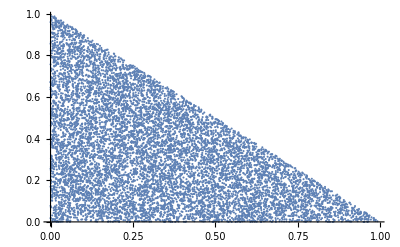

```mathematica
ListPlot@Table[RandomDistr[3][[1;;2]],10000]
```

```mathematica
ListPointPlot3D@Table[RandomDistr[4][[1;;3]],3000]
```

-Graphics3D-

```mathematica
And@@Table[IsDistr[RandomDistr[testdim]],100]
```

True

```mathematica
And@@Table[IsDistr[RandomA[testdim].RandomDistr[testdim]],1000]
```

True

The following lets Mathematica show symbolically that constantA works as intended, i.e., that constantA[q].p=q for any distributions q and p.

```mathematica
Clear[q];FullSimplify[ConstantA[Array[q,testdim]].Array[p,testdim],IsDistr[Array[p,testdim]]]==Array[q,testdim]
```

True

Scoring rules

```mathematica
-0.23<=LogScore[{0.8,0.2},{1,0}]<=-0.21
```

True

Log scoring rule degenerate cases

```mathematica
Simplify[logscoreh[0,x],x>0]==-∞
```

True

```mathematica
logscoreh[1,0]==0
```

True

```mathematica
logscoreh[0,0]==0
```

True

```mathematica
LogScore[{1,0,0},{1,0,0}]==0
```

True

```mathematica
LogScore[{1/2,1/2,0},uniform[3]]==-∞
```

True

Propriety

We here test that the scoring rules we defined are indeed proper. We do this specifically by making sure that if the environment probability is a fixed distribution q, then the optimal report is q.

LogScore:

```mathematica
Clear[p];N[Last/@Last@Maximize[LogScore[Array[p,testdim],uniform[testdim]],IsDistr[Array[p,testdim]],Array[p,testdim]]]==uniform[testdim]
```

True

```mathematica
Clear[p];AbsoluteTiming[trueFraction@Table[q=RandomDistr[testdim];N@Last/@Last@Maximize[LogScore[Array[p,testdim],q],IsDistr[Array[p,testdim]],Array[p,testdim]]==N@q,500]]
```

{61.6183,497/500}

```mathematica
AbsoluteTiming[trueFraction@Table[q=RandomDistr[testdim];N/@Last/@Last@Maximize[LogScore[Array[p,testdim],q],IsDistr[Array[p,testdim]],Array[p,testdim]]==q,1000]]
```

{124.967,124/125}

BrierScore:

```mathematica
Clear[p];N[Last/@Last@Maximize[BrierScore[Array[p,testdim],uniform[testdim]],IsDistr[Array[p,testdim]],Array[p,testdim]]]==uniform[testdim]
```

True

```mathematica
AbsoluteTiming[trueFraction@Table[q=RandomDistr[testdim];N[Last/@Last@Maximize[BrierScore[Array[p,testdim],q],IsDistr[Array[p,testdim]],Array[p,testdim]]]==q,100]]
```

{3.53072,1}

Finding fixed points

```mathematica
AbsoluteTiming[And@@Table[q=RandomDistr[testdim];FixedPointDistr[ConstantA[q]]==q,5000]]
```

{38.9569,True}

```mathematica
AbsoluteTiming[And@@Table[IsDistr[FixedPointDistr[RandomA[testdim]]],1000]]
```

{8.45286,True}

```mathematica
AbsoluteTiming[And@@Table[A=RandomA[testdim];p=FixedPointDistr[A];A.p==p,1000]]
```

{8.70124,True}

Optimal report function

Optimal reports should be probability distributions.

LogScore:

```mathematica
AbsoluteTiming[And@@Table[IsDistr[OptReportN[LogScore,RandomA[testdim]]],10]]
```

{11.4737,True}

BrierScore:

```mathematica
AbsoluteTiming[And@@Table[IsDistrAppr[OptReportN[BrierScore,RandomA[testdim]]],10]]
```

{57.4924,True}

```mathematica
AbsoluteTiming[And@@Table[IsDistrAppr[OptReportBrier[RandomA[testdim]]],5]]
```

{22.8389,True}

On randomly generated A, I test whether the “optimal report” is at least as good as the fixed point.

LogScore:

```mathematica
AbsoluteTiming[And@@Table[A=RandomA[testdim];p=OptReportN[LogScore,A];fp=FixedPointDistr[A];LogScore[p,A.p]>=LogScore[fp,fp],10]]
```

{12.0896,True}

BrierScore:

```mathematica
AbsoluteTiming[And@@Table[A=RandomA[testdim];p=OptReportN[BrierScore,A];fp=FixedPointDistr[A];BrierScore[p,A.p]>=BrierScore[fp,fp],5]]
```

{17.3342,True}

```mathematica
AbsoluteTiming[And@@Table[A=RandomA[testdim];p=OptReportBrier[A];fp=FixedPointDistr[A];BrierScore[p,A.p]>=BrierScore[fp,fp],10]]
```

{46.9396,True}

On randomly generated A, I test whether the “optimal report” (as found by OptReport) is at least as good as a bunch of randomly generated reports.

LogScore:

```mathematica
AbsoluteTiming[And@@Table[A=RandomA[testdim];p=OptReportN[LogScore,A];
And@@Table[randp=RandomDistr[testdim];
LogScore[p,A.p]>=LogScore[randp,A.randp],5000],10]]
```

{33.1812,True}

BrierScore:

```mathematica
AbsoluteTiming[And@@Table[A=RandomA[testdim];p=OptReportN[BrierScore,A];
And@@Table[randp=RandomDistr[testdim];
BrierScore[p,A.p]>=BrierScore[randp,A.randp],5000],10]]
```

{67.5161,True}

```mathematica
AbsoluteTiming[And@@Table[A=RandomA[testdim];p=OptReportBrier[A];
And@@Table[randp=RandomDistr[testdim];
BrierScore[p,A.p]>=BrierScore[randp,A.randp],10000],5]]
```

{52.1098,True}

If A is simply the matrix that maps each probability distribution onto q, then the optimal report should be approximately q.

LogScore:

```mathematica
AbsoluteTiming[And@@Table[q=RandomDistr[testdim];p=OptReportN[LogScore,ConstantA[q]];Norm[p-q]<=0.00001,10]]
```

{10.0449,True}

BrierScore:

```mathematica
AbsoluteTiming[And@@Table[q=RandomDistr[testdim];p=OptReportN[BrierScore,ConstantA[q]];Norm[p-q]<=0.00001,10]]
```

{12.3352,True}

```mathematica
AbsoluteTiming[And@@Table[q=RandomDistr[testdim];p=OptReportBrier[ConstantA[q]];p==q,100]]
```

{35.4246,True}

We can now test the NMaximized-based approximate best report function against the Maximize-based exact best report function for the Brier scoring rule.

```mathematica
AbsoluteTiming[trueFraction@Table[A=RandomA[3];p1=OptReportBrier[A];p2=OptReportN[BrierScore,A];Norm[p1-p2]<=0.001,10]]
```

{36.3606,9/10}

```mathematica
AbsoluteTiming[trueFraction@Table[A=RandomA[4];p1=OptReportBrier[A];p2=OptReportN[BrierScore,A];Norm[p1-p2]<=0.001,8]]
```

{45.2624,7/8}

```mathematica
AbsoluteTiming[trueFraction@Table[A=RandomA[5];p1=OptReportBrier[A];p2=OptReportN[BrierScore,A];Norm[p1-p2]<=0.001,3]]
```

{25.1192,1}

Experiment

```mathematica
S=BrierScore;
```

```mathematica
dim=5;
```

We sample n matrices A. For each of them we record four numbers: 1) the operator norm of A; 2) how far the fixed point distribution of A is from the uniform distribution; 3) how far the optimal report is from the fixed point; 4) how far the optimal report is from the true distribution when the optimal report is made; 5) how far the actual report is from the uniform distribution.

```mathematica
data={};
```

```mathematica
AbsoluteTiming[data=Union[data,ParallelTable[TimeConstrained[A=RandomA[dim];
fixedpoint=FixedPointDistr[A];
optrep=OptReportBrier[A];{N@TangentSpaceOpNormN[A],N@Norm[fixedpoint-uniform[dim]],N@Norm[optrep-fixedpoint],N@Norm[optrep-A.optrep],N@Norm[optrep-uniform[dim]]},120,"NT"],1000],SameTest->(False&)]]
```

{2478.22,{NT,NT,NT,NT,NT,NT,NT,NT,NT,NT,NT,NT,NT,NT,NT,NT,NT,NT,NT,NT,NT,NT,NT,NT,NT,NT,NT,NT,NT,NT,NT,NT,NT,NT,NT,NT,NT,NT,NT,NT,NT,NT,NT,NT,NT,NT,NT,NT,NT,{0.280956,0.252549,0.0519778,0.0593722,0.236125},{0.286872,0.13521,0.0138981,0.0140218,0.146248},{0.301215,0.13723,0.0176383,0.0207449,0.122175},{0.302033,0.196317,0.048789,0.0432522,0.226451},{0.306947,0.207128,0.0916818,0.071576,0.292457},{0.308966,0.204604,0.0924591,0.0685626,0.278452},{0.311143,0.207818,0.0568528,0.0549765,0.236614},{0.320429,0.149182,0.0306623,0.0338356,0.148156},{0.324061,0.113301,0.0356888,0.0287619,0.141601},{0.327079,0.125667,0.0390113,0.0345866,0.126096},{0.327517,0.222483,0.064568,0.0533106,0.255123},{0.328159,0.152232,0.0252615,0.0295684,0.15812},{0.331014,0.225257,0.0650697,0.0512257,0.267893},{0.334634,0.241837,0.0499509,0.0484198,0.269886},{0.337816,0.102245,0.0203449,0.0226204,0.104911},{0.338311,0.200523,0.103534,0.0776103,0.300311},{0.340797,0.0621041,0.00979671,0.00935667,0.0575311},{0.341368,0.134714,0.0238568,0.0265766,0.120155},{0.342093,0.207807,0.0577535,0.0537164,0.251976},{0.342617,0.140695,0.033223,0.0267847,0.163066},{0.343993,0.224689,0.121035,0.0905599,0.343656},{0.351312,0.123603,0.0230309,0.0273123,0.106246},{0.352546,0.336164,0.138512,0.112448,0.452267},{0.353629,0.125933,0.0338642,0.0356467,0.119979},{0.35493,0.0725009,0.0259008,0.0227499,0.0828751},{0.361327,0.12963,0.0848974,0.0669758,0.203065},{0.361641,0.0942288,0.0600125,0.0447943,0.134144},{0.361847,0.139257,0.0651085,0.0530098,0.19092},{0.362146,0.258241,0.0413917,0.0428755,0.239659},{0.363862,0.251,0.0927862,0.0747902,0.318195},{0.36544,0.280272,0.0715756,0.0811306,0.263387},{0.366985,0.14814,0.0662507,0.0554422,0.202094},{0.367996,0.136175,0.104932,0.0771102,0.218934},{0.368825,0.167446,0.0640822,0.0499741,0.206449},{0.369258,0.159942,0.0445372,0.0414369,0.166364},{0.37024,0.206691,0.0676108,0.0575271,0.269439},{0.370362,0.0978758,0.0390101,0.0344295,0.115339},{0.370422,0.146976,0.0447289,0.0453832,0.167095},{0.371308,0.0945403,0.0212011,0.0223986,0.0879257},{0.372238,0.138517,0.0446546,0.0441748,0.158587},{0.374706,0.246674,0.034765,0.0406201,0.226143},{0.375967,0.127989,0.0225535,0.0228942,0.138039},{0.376253,0.163563,0.0253331,0.0274187,0.174419},{0.376375,0.115241,0.0301944,0.0231614,0.125078},{0.378225,0.20855,0.0758295,0.0682808,0.267188},{0.378679,0.114674,0.0543802,0.0466323,0.159035},{0.380122,0.172282,0.147923,0.105463,0.293707},{0.384311,0.29847,0.168082,0.135968,0.445309},{0.384885,0.204531,0.0291466,0.0290584,0.212764},{0.385715,0.191472,0.0647224,0.0484782,0.235992},{0.38601,0.197515,0.0369843,0.0375747,0.215629},{0.387916,0.242137,0.0665315,0.0661624,0.253652},{0.387995,0.176309,0.106949,0.0762149,0.256134},{0.388342,0.211464,0.0679658,0.0703973,0.223059},{0.389473,0.121316,0.0473703,0.0396954,0.151634},{0.390487,0.172586,0.091304,0.0666064,0.257657},{0.391083,0.208913,0.0426567,0.0492229,0.214658},{0.391992,0.133685,0.0241065,0.0274423,0.118415},{0.395088,0.128959,0.155755,0.102702,0.275585},{0.39526,0.251766,0.135639,0.119263,0.366967},{0.395264,0.114739,0.0903535,0.0621447,0.196309},{0.396433,0.22857,0.157723,0.117174,0.351843},{0.398391,0.165364,0.0490458,0.0334819,0.161132},{0.398583,0.0881945,0.0403803,0.0362734,0.111673},{0.398638,0.204767,0.0294587,0.0329278,0.216162},{0.400537,0.154574,0.0813686,0.0560201,0.17992},{0.400654,0.0681195,0.0583321,0.041085,0.118903},{0.402289,0.0822457,0.0166706,0.0164131,0.0807385},{0.402708,0.0940482,0.024438,0.0277321,0.086548},{0.404001,0.181415,0.041034,0.0467321,0.175397},{0.40423,0.178687,0.0205196,0.0212631,0.171962},{0.405364,0.288778,0.0413897,0.0460621,0.266606},{0.406052,0.148476,0.0495749,0.0427374,0.142179},{0.406822,0.241438,0.0754417,0.061866,0.294036},{0.407477,0.142824,0.0458067,0.0383729,0.165802},{0.408328,0.105683,0.0214231,0.0229764,0.109096},{0.409686,0.103396,0.0475571,0.0368822,0.150303},{0.411648,0.194341,0.0552476,0.0500969,0.232526},{0.412323,0.174785,0.0308152,0.0358965,0.163074},{0.412417,0.17047,0.0667455,0.0508462,0.200887},{0.413647,0.265888,0.12875,0.109161,0.383994},{0.414366,0.262807,0.091832,0.0745859,0.316757},{0.415527,0.158248,0.0577529,0.0464962,0.165079},{0.417966,0.101648,0.0196643,0.0216728,0.0942526},{0.418736,0.231401,0.0724054,0.0631969,0.274597},{0.418757,0.20243,0.171963,0.114599,0.343205},{0.419365,0.0534231,0.0149352,0.0145585,0.0495659},{0.421178,0.118202,0.103553,0.0668594,0.194913},{0.421409,0.125044,0.0953829,0.0701446,0.181195},{0.422136,0.124653,0.00838455,0.00998708,0.127135},{0.425589,0.154592,0.0301442,0.025891,0.178053},{0.425908,0.21956,0.0507817,0.0410153,0.260789},{0.426466,0.229337,0.253525,0.157234,0.44489},{0.426674,0.100361,0.0440134,0.0321567,0.117286},{0.427407,0.0831082,0.0212449,0.020278,0.0868431},{0.427478,0.181845,0.103499,0.0695439,0.2618},{0.42868,0.151762,0.0607717,0.0510658,0.174594},{0.430212,0.197904,0.181409,0.123224,0.30792},{0.430351,0.109563,0.0461927,0.0412619,0.139816},{0.43064,0.263347,0.154941,0.136273,0.373658},{0.430946,0.181507,0.111087,0.07462,0.272744},{0.431086,0.164785,0.232273,0.140861,0.373176},{0.431576,0.0908246,0.0106933,0.0128282,0.0946967},{0.431815,0.121969,0.0576077,0.044286,0.166757},{0.432785,0.0471608,0.0468903,0.0327992,0.0922631},{0.434662,0.172756,0.0779372,0.0619064,0.223373},{0.435086,0.235827,0.0471994,0.0522952,0.252517},{0.435531,0.135433,0.178711,0.116888,0.307227},{0.436018,0.0307517,0.0143799,0.0133396,0.0341695},{0.436902,0.135799,0.162634,0.100793,0.272849},{0.437553,0.156215,0.106602,0.0811359,0.233729},{0.438052,0.150534,0.0204309,0.0214662,0.136473},{0.438228,0.153867,0.189962,0.118704,0.319142},{0.438379,0.30322,0.242519,0.173025,0.523305},{0.439088,0.0269433,0.00792838,0.00856456,0.0262034},{0.439151,0.0595925,0.0152991,0.0193717,0.0513702},{0.439824,0.138192,0.161712,0.102126,0.252968},{0.440725,0.119016,0.0430778,0.0347302,0.153392},{0.441143,0.116355,0.0476958,0.0440171,0.125605},{0.441665,0.121812,0.0253486,0.0295242,0.106973},{0.441941,0.24396,0.118118,0.0990563,0.274071},{0.442106,0.128629,0.0523283,0.0402685,0.157727},{0.442408,0.141064,0.0899239,0.0709799,0.210743},{0.443297,0.229502,0.051446,0.0461827,0.217067},{0.444153,0.104763,0.0953443,0.070077,0.171263},{0.44423,0.166782,0.0520936,0.056836,0.192592},{0.444231,0.150382,0.0305443,0.0304931,0.152027},{0.444754,0.204521,0.0715202,0.0606869,0.240681},{0.445273,0.222705,0.341671,0.20366,0.549633},{0.445584,0.118776,0.0658594,0.0504919,0.179516},{0.446418,0.0929607,0.0466592,0.0297513,0.115953},{0.448127,0.111017,0.0234558,0.0269431,0.118378},{0.448304,0.243103,0.258302,0.190791,0.441497},{0.448505,0.0905321,0.0103142,0.0131352,0.0819325},{0.44875,0.209414,0.0590857,0.0716349,0.197953},{0.449622,0.0675543,0.0366272,0.032268,0.0869324},{0.449974,0.221163,0.159181,0.115747,0.345732},{0.450463,0.123629,0.0278115,0.0263392,0.14765},{0.450688,0.0825639,0.0176053,0.0197436,0.0755103},{0.45096,0.0774329,0.0328809,0.0231046,0.103478},{0.4511,0.100977,0.0178555,0.0173943,0.102632},{0.451579,0.138688,0.0336882,0.0377899,0.144601},{0.451829,0.191565,0.11083,0.0784807,0.25737},{0.453088,0.198498,0.0513528,0.0457984,0.24726},{0.453728,0.194653,0.0443355,0.0374799,0.207126},{0.454065,0.234216,0.222552,0.142829,0.456044},{0.455278,0.0702138,0.0531194,0.0320024,0.100142},{0.455902,0.158084,0.0332006,0.0255934,0.183287},{0.456176,0.0610255,0.0228213,0.0247578,0.0690506},{0.456712,0.177787,0.318648,0.181711,0.464509},{0.457158,0.0753515,0.0192313,0.0204204,0.0652455},{0.457533,0.107197,0.0519807,0.0401577,0.154339},{0.457678,0.198836,0.0776772,0.0699424,0.269103},{0.457692,0.0962247,0.054444,0.0464419,0.123053},{0.457832,0.272198,0.12099,0.0986269,0.378508},{0.457922,0.158294,0.258134,0.165125,0.388957},{0.458043,0.133581,0.0309819,0.0372711,0.108247},{0.458159,0.10515,0.0271736,0.0242391,0.10667},{0.458343,0.198766,0.068737,0.0636398,0.200193},{0.458422,0.12104,0.0288502,0.0286116,0.116049},{0.458873,0.155208,0.0771687,0.0615422,0.210499},{0.459481,0.169285,0.349937,0.215229,0.480135},{0.459566,0.0515254,0.0269781,0.0245387,0.0644526},{0.459569,0.134288,0.161539,0.092594,0.254793},{0.459607,0.120122,0.024232,0.0190095,0.117941},{0.45963,0.0983867,0.0290541,0.0216737,0.104235},{0.459851,0.137393,0.0665615,0.0602219,0.152993},{0.459928,0.0736359,0.0219869,0.0261253,0.0761524},{0.460211,0.15015,0.0280029,0.0331796,0.156013},{0.460299,0.143924,0.0909042,0.0751956,0.186852},{0.460322,0.110267,0.0309866,0.0333163,0.100437},{0.460507,0.101567,0.0355825,0.0309208,0.119029},{0.460545,0.126909,0.0699492,0.0589219,0.166572},{0.460908,0.113228,0.0269265,0.0254617,0.126429},{0.461297,0.129343,0.0364866,0.038415,0.12418},{0.462,0.115449,0.0398684,0.0315101,0.120056},{0.46214,0.211458,0.137138,0.10639,0.281625},{0.462804,0.141557,0.0416063,0.0377775,0.151031},{0.462867,0.0951462,0.0498404,0.0407907,0.105528},{0.464022,0.121134,0.0282744,0.0290559,0.119077},{0.464077,0.102896,0.0922602,0.0639991,0.157437},{0.464874,0.100876,0.0824244,0.0560588,0.161996},{0.465352,0.150502,0.0779072,0.0496726,0.183335},{0.46556,0.100174,0.0676685,0.0490138,0.139558},{0.46561,0.152649,0.0567933,0.055253,0.185412},{0.465699,0.123814,0.0421945,0.0355845,0.162231},{0.466318,0.175183,0.0347849,0.034746,0.172162},{0.466663,0.156292,0.118608,0.0772483,0.22651},{0.467133,0.220337,0.0840948,0.0659024,0.293388},{0.467342,0.223105,0.0504559,0.0530754,0.194797},{0.467474,0.176963,0.140794,0.11278,0.289252},{0.467772,0.161329,0.0646635,0.0508891,0.209396},{0.46784,0.132486,0.134691,0.105076,0.24189},{0.46869,0.133537,0.0270128,0.0300531,0.142204},{0.46871,0.114632,0.0710481,0.0628548,0.178725},{0.469991,0.309585,0.116382,0.0919844,0.387848},{0.470529,0.150341,0.0269439,0.0283559,0.155378},{0.470769,0.158931,0.0546604,0.0489479,0.176613},{0.470787,0.101655,0.0608935,0.0422053,0.155528},{0.470799,0.258424,0.0949624,0.0874359,0.318666},{0.471224,0.181919,0.207525,0.130392,0.317383},{0.471428,0.212421,0.264914,0.177947,0.475023},{0.471475,0.133409,0.0694962,0.0665543,0.17788},{0.471977,0.223717,0.113591,0.0901566,0.333974},{0.472167,0.134821,0.046798,0.0333151,0.142404},{0.473323,0.0890535,0.0354841,0.0352414,0.117547},{0.473474,0.143422,0.12694,0.0817341,0.206148},{0.474001,0.12737,0.0314825,0.0350494,0.114983},{0.474678,0.151512,0.242771,0.13954,0.372885},{0.47472,0.146483,0.0822376,0.0601103,0.226305},{0.474764,0.101116,0.0539483,0.0411532,0.116001},{0.475012,0.2088,0.443672,0.264223,0.609423},{0.475161,0.0849033,0.0305672,0.0345052,0.0833956},{0.476539,0.169543,0.0248134,0.0322217,0.163972},{0.476695,0.180963,0.0683547,0.0592416,0.191004},{0.476951,0.13144,0.144173,0.10023,0.259831},{0.476985,0.124718,0.109626,0.0749638,0.227237},{0.477307,0.0730115,0.0230905,0.0211127,0.0720668},{0.478009,0.0831601,0.0749124,0.0517395,0.147443},{0.478227,0.149465,0.0417316,0.0366073,0.170279},{0.478323,0.100125,0.121309,0.0813053,0.21484},{0.478508,0.168906,0.190683,0.12832,0.347504},{0.478768,0.0515851,0.0139653,0.0144513,0.0552479},{0.479233,0.150398,0.0860902,0.0810561,0.180885},{0.479723,0.0759531,0.0344688,0.0319534,0.0848989},{0.479824,0.134503,0.0519887,0.0484866,0.145288},{0.479897,0.133087,0.0609395,0.0461193,0.183711},{0.48028,0.157459,0.039808,0.032355,0.169212},{0.480452,0.167838,0.0675058,0.0567508,0.20395},{0.480817,0.138499,0.0702174,0.0704934,0.178167},{0.481721,0.14221,0.0688618,0.0548375,0.194756},{0.481881,0.215458,0.098103,0.0913444,0.298474},{0.482118,0.126853,0.0667308,0.0651586,0.149711},{0.482339,0.213734,0.503888,0.287326,0.686915},{0.482439,0.0645768,0.00486434,0.00534917,0.0601087},{0.482445,0.082832,0.0348652,0.0329408,0.0910146},{0.482474,0.172508,0.397439,0.220591,0.525677},{0.482753,0.117083,0.100132,0.081309,0.192135},{0.483891,0.319151,0.271701,0.193181,0.578145},{0.483943,0.184557,0.0370201,0.0408805,0.209577},{0.485165,0.254438,0.065829,0.0564434,0.272973},{0.485223,0.128128,0.0324224,0.0269492,0.146962},{0.485609,0.207337,0.272197,0.180708,0.3966},{0.485779,0.235257,0.0746889,0.0808209,0.233394},{0.48698,0.222127,0.297418,0.163923,0.472082},{0.487044,0.203683,0.0940782,0.0684201,0.270527},{0.487535,0.179873,0.0475978,0.0558025,0.155646},{0.4883,0.221781,0.221526,0.172664,0.417334},{0.488507,0.140498,0.0783747,0.0550978,0.185726},{0.488517,0.20258,0.0637963,0.0677668,0.185317},{0.488531,0.170826,0.243798,0.138925,0.369681},{0.488591,0.174273,0.118652,0.0878592,0.245316},{0.488959,0.0998083,0.0649581,0.049965,0.1296},{0.489234,0.144364,0.0416159,0.0363372,0.162123},{0.489346,0.107428,0.0554829,0.0416081,0.153681},{0.489773,0.0831948,0.018007,0.0182884,0.0813212},{0.490221,0.157896,0.101401,0.0695554,0.214143},{0.490261,0.122341,0.0265332,0.0314829,0.133681},{0.490572,0.103072,0.118549,0.0777202,0.205136},{0.490953,0.235471,0.0620457,0.0450874,0.238352},{0.491136,0.121496,0.12466,0.0760963,0.221636},{0.491399,0.194072,0.46226,0.257213,0.637738},{0.491625,0.125167,0.0349154,0.0307119,0.135781},{0.491661,0.207562,0.0650477,0.0603345,0.261736},{0.492244,0.100431,0.028842,0.0361085,0.0961362},{0.492418,0.114641,0.122758,0.0880142,0.212748},{0.492713,0.212349,0.228548,0.138926,0.426125},{0.494051,0.16954,0.136819,0.1036,0.266661},{0.494227,0.0941875,0.0110651,0.0139072,0.0979085},{0.49523,0.139947,0.0250249,0.030523,0.127635},{0.495584,0.236751,0.11655,0.0806367,0.269159},{0.495678,0.104924,0.0588311,0.0492392,0.157223},{0.497194,0.156173,0.0490848,0.039689,0.193307},{0.498326,0.197026,0.177328,0.122092,0.326786},{0.498476,0.100275,0.0209409,0.022893,0.110163},{0.498814,0.0698554,0.0161337,0.0179045,0.0647218},{0.498858,0.189967,0.0774849,0.0727357,0.214385},{0.498859,0.218373,0.0617913,0.0546417,0.263014},{0.499719,0.120772,0.0400953,0.0462085,0.137495},{0.499817,0.0916629,0.0320238,0.0261613,0.0981134},{0.501148,0.170156,0.497699,0.272632,0.640936},{0.501421,0.213693,0.0959902,0.0755416,0.233154},{0.502177,0.0594054,0.0142304,0.0170324,0.0485577},{0.502199,0.0301678,0.0112625,0.0102511,0.0296159},{0.50244,0.0995667,0.0301773,0.0377294,0.0850982},{0.502497,0.183694,0.0386814,0.0359152,0.19572},{0.502592,0.139109,0.253945,0.141881,0.328769},{0.502633,0.141339,0.154905,0.105971,0.287799},{0.503221,0.205285,0.0746457,0.0538273,0.277656},{0.503499,0.0704954,0.0195474,0.0186209,0.0764315},{0.503515,0.228718,0.203273,0.150111,0.382022},{0.503904,0.121056,0.222224,0.140037,0.338708},{0.504072,0.223655,0.286848,0.176237,0.498329},{0.50442,0.185222,0.0437391,0.0551046,0.17223},{0.504577,0.0826605,0.174916,0.108122,0.254467},{0.505833,0.320039,0.313053,0.199603,0.627527},{0.505914,0.191404,0.0561009,0.0639729,0.212951},{0.506348,0.0789516,0.0404364,0.0389583,0.109242},{0.506857,0.190422,0.072195,0.0645103,0.238346},{0.506934,0.114914,0.0256485,0.0265781,0.119968},{0.506979,0.12614,0.110356,0.0802687,0.210531},{0.508582,0.111388,0.0705395,0.0631678,0.136613},{0.509013,0.286166,0.0942095,0.103981,0.337508},{0.509075,0.0755428,0.0146117,0.0177377,0.0731289},{0.509703,0.103732,0.0371756,0.0373328,0.120937},{0.50977,0.16314,0.252766,0.163431,0.413822},{0.510138,0.182894,0.0325814,0.0228849,0.196124},{0.510174,0.0946251,0.0104724,0.0140288,0.0872955},{0.510428,0.112513,0.0377779,0.0362345,0.118203},{0.510546,0.133098,0.20887,0.139498,0.331629},{0.510734,0.12897,0.0365998,0.0289135,0.161452},{0.510968,0.191309,0.159859,0.123295,0.340772},{0.511288,0.226326,0.126455,0.0862738,0.316224},{0.511305,0.213997,0.0156386,0.0164592,0.217385},{0.511823,0.109178,0.158498,0.102129,0.224769},{0.512163,0.118318,0.095349,0.0705835,0.211077},{0.512295,0.12576,0.163555,0.0934147,0.274514},{0.512345,0.160023,0.1454,0.091238,0.277364},{0.51235,0.176718,0.172848,0.128708,0.321008},{0.513455,0.315294,0.408275,0.259444,0.688289},{0.513618,0.135874,0.0210513,0.0237195,0.119441},{0.514677,0.135309,0.0737953,0.0634846,0.20147},{0.514697,0.140151,0.0857072,0.0629172,0.218371},{0.51519,0.100297,0.227922,0.12324,0.280139},{0.516235,0.185223,0.315926,0.187207,0.494842},{0.516464,0.166765,0.598445,0.317014,0.629899},{0.516621,0.177834,0.146401,0.113849,0.306147},{0.51681,0.149889,0.131966,0.105689,0.220362},{0.516905,0.107198,0.142743,0.087299,0.236477},{0.516909,0.1452,0.0311487,0.0412825,0.124575},{0.517242,0.185197,0.123741,0.0945588,0.292988},{0.517275,0.136761,0.040694,0.0370395,0.172124},{0.517288,0.0513614,0.163402,0.0913829,0.198489},{0.517386,0.0722964,0.0287953,0.0241103,0.0794972},{0.517639,0.102719,0.0598883,0.0490764,0.150653},{0.518005,0.169459,0.049369,0.0486202,0.166469},{0.518172,0.1077,0.0359376,0.0393806,0.0970099},{0.518551,0.0605183,0.0184762,0.0239094,0.0495721},{0.518847,0.134606,0.0234584,0.0244695,0.126832},{0.519931,0.0913492,0.029083,0.0348536,0.0883485},{0.520343,0.184863,0.167837,0.114062,0.333846},{0.520455,0.185202,0.0882886,0.0626531,0.241964},{0.520859,0.192761,0.110656,0.0970865,0.286748},{0.521554,0.115437,0.0430647,0.0471577,0.136752},{0.521656,0.22732,0.156068,0.123365,0.362422},{0.521704,0.180228,0.0117625,0.0146188,0.174861},{0.521712,0.109519,0.0279735,0.0352938,0.110352},{0.521882,0.139423,0.0672655,0.0630145,0.1669},{0.522776,0.173065,0.0575904,0.0529106,0.208688},{0.52282,0.0724777,0.0764283,0.0543976,0.140844},{0.523172,0.0855661,0.0288009,0.0273267,0.0825059},{0.523713,0.131718,0.0663928,0.0579081,0.160325},{0.523839,0.121355,0.0432403,0.0503846,0.124826},{0.523893,0.201792,0.170858,0.14088,0.352684},{0.524298,0.169756,0.0837524,0.0599174,0.207288},{0.524483,0.110306,0.068812,0.0566472,0.130248},{0.524841,0.138724,0.0676316,0.0600697,0.160125},{0.52487,0.0720657,0.0266882,0.0312979,0.073364},{0.524953,0.124596,0.136781,0.0982827,0.244818},{0.524957,0.093344,0.0742035,0.0502427,0.161851},{0.525216,0.0677466,0.0356596,0.0322311,0.0902141},{0.525543,0.205069,0.133453,0.110293,0.287063},{0.526644,0.254915,0.168393,0.143053,0.409417},{0.527075,0.289241,0.130337,0.103729,0.39873},{0.527088,0.281565,0.0942344,0.0946934,0.343433},{0.527179,0.243734,0.0356225,0.0423188,0.22168},{0.527232,0.0809283,0.0630878,0.0498401,0.121409},{0.527352,0.10714,0.0340427,0.0428417,0.116438},{0.527699,0.203958,0.243575,0.145303,0.417707},{0.528199,0.213785,0.639459,0.342989,0.779305},{0.528707,0.154212,0.145717,0.102311,0.282267},{0.529015,0.125437,0.0219524,0.0300723,0.127811},{0.529337,0.125614,0.396325,0.222111,0.511238},{0.529694,0.244336,0.0789266,0.0783179,0.309261},{0.52979,0.215724,0.454046,0.238243,0.594577},{0.529832,0.485408,0.411611,0.251698,0.894427},{0.530194,0.141641,0.188882,0.103202,0.267824},{0.530508,0.0623711,0.0234878,0.0219597,0.0565834},{0.530605,0.174079,0.0636719,0.0534891,0.199091},{0.530851,0.0925822,0.0193083,0.0246147,0.0960457},{0.531008,0.0897706,0.016721,0.0154565,0.101814},{0.531012,0.166112,0.100682,0.0804776,0.249698},{0.53108,0.162693,0.0467395,0.0425722,0.19886},{0.531446,0.119768,0.0369476,0.0322789,0.151982},{0.531774,0.077296,0.022696,0.0138204,0.0867075},{0.531834,0.201159,0.251451,0.148781,0.42836},{0.532008,0.121589,0.126157,0.0946022,0.183292},{0.532379,0.171832,0.130379,0.1175,0.231738},{0.53275,0.309729,0.100451,0.0896736,0.402646},{0.532821,0.198261,0.239391,0.149566,0.430825},{0.533323,0.155412,0.0589642,0.0715819,0.171258},{0.533649,0.145075,0.263106,0.157475,0.384778},{0.533777,0.132286,0.0475421,0.0418859,0.16939},{0.534185,0.162191,0.353612,0.212488,0.512821},{0.534421,0.258871,0.152941,0.110686,0.396384},{0.534626,0.121238,0.0883954,0.0627214,0.202679},{0.534984,0.0633133,0.0204821,0.0178381,0.0815042},{0.536367,0.164561,0.0418564,0.0476055,0.131617},{0.536563,0.190897,0.276463,0.161216,0.374129},{0.53657,0.354663,0.171514,0.124815,0.522026},{0.53688,0.16679,0.14487,0.099449,0.298943},{0.536945,0.11346,0.125548,0.0923191,0.226657},{0.537202,0.0829076,0.361527,0.189881,0.423276},{0.537345,0.246758,0.315259,0.199674,0.535853},{0.537385,0.142913,0.105182,0.0705128,0.231319},{0.538045,0.177219,0.0799941,0.0824912,0.23735},{0.538053,0.283182,0.236167,0.192671,0.469798},{0.538436,0.0435907,0.0125316,0.0130042,0.049733},{0.538607,0.253599,0.0272831,0.0319394,0.228049},{0.53878,0.157432,0.0739744,0.0689887,0.201761},{0.538819,0.126069,0.0806379,0.049861,0.182312},{0.539046,0.296359,0.0586843,0.0682563,0.334743},{0.539089,0.0996785,0.336888,0.175822,0.399628},{0.539166,0.123488,0.0335738,0.0375477,0.136534},{0.539226,0.121696,0.0483128,0.0366476,0.139622},{0.539371,0.123136,0.60477,0.327884,0.674593},{0.540174,0.0865303,0.0197984,0.0231658,0.0865022},{0.540778,0.147813,0.0869305,0.0847889,0.182945},{0.540952,0.125361,0.0828694,0.0544133,0.175561},{0.542201,0.248825,0.208447,0.185094,0.425378},{0.542262,0.107731,0.256087,0.153896,0.294246},{0.542544,0.198172,0.709672,0.367176,0.894427},{0.542753,0.232907,0.0714943,0.0789643,0.242527},{0.5431,0.413763,0.497583,0.287753,0.894427},{0.543226,0.0742477,0.0390251,0.0343653,0.100789},{0.543451,0.0842456,0.075861,0.0524957,0.115363},{0.544148,0.137576,0.223004,0.154897,0.339521},{0.544229,0.0822709,0.0385382,0.0395206,0.0771067},{0.544297,0.109088,0.0506932,0.0491317,0.137243},{0.544456,0.291717,0.599623,0.36324,0.860818},{0.545777,0.177547,0.236292,0.150989,0.357385},{0.54595,0.12358,0.0247428,0.0194439,0.140719},{0.545983,0.254789,0.133953,0.107059,0.322317},{0.546184,0.156711,0.0501265,0.0286675,0.175035},{0.546184,0.0754854,0.0222206,0.029435,0.0685652},{0.547269,0.0715494,0.0282538,0.0298976,0.0883988},{0.54769,0.273723,0.166101,0.123036,0.410362},{0.547728,0.114508,0.153759,0.0912122,0.228617},{0.547733,0.318888,0.258234,0.15324,0.563143},{0.548006,0.145427,0.120967,0.0823487,0.238659},{0.548306,0.0871903,0.0530372,0.0525514,0.118453},{0.548411,0.278335,0.186596,0.159645,0.413533},{0.549229,0.170938,0.0691491,0.0560433,0.228984},{0.54984,0.154731,0.0822627,0.07044,0.22615},{0.550049,0.107107,0.0219171,0.0228236,0.114152},{0.550901,0.105199,0.0602063,0.0555871,0.146662},{0.55098,0.160673,0.0465044,0.0463292,0.170727},{0.550992,0.154297,0.140709,0.103204,0.245496},{0.551547,0.267444,0.246962,0.205422,0.470241},{0.552076,0.302245,0.27423,0.175429,0.562323},{0.552686,0.159499,0.54923,0.284855,0.638892},{0.552688,0.112376,0.027108,0.0248643,0.133969},{0.55312,0.128302,0.284892,0.142431,0.322375},{0.553244,0.141726,0.0827651,0.0638174,0.192226},{0.553248,0.132843,0.488844,0.268728,0.528962},{0.553329,0.118868,0.0340396,0.0428845,0.113117},{0.553793,0.154729,0.0319031,0.0399848,0.158609},{0.554017,0.095694,0.0249012,0.0201103,0.0913249},{0.554414,0.137986,0.178037,0.106442,0.292841},{0.554758,0.165823,0.18202,0.119391,0.34345},{0.554974,0.0990985,0.040353,0.0367273,0.123348},{0.555167,0.0915864,0.0324147,0.0296865,0.0875405},{0.555169,0.150319,0.10898,0.0917052,0.206336},{0.555232,0.110889,0.0360635,0.0337843,0.142668},{0.555295,0.319575,0.293789,0.18605,0.536743},{0.555388,0.225023,0.274394,0.170954,0.490419},{0.555459,0.191875,0.0235761,0.0292343,0.201911},{0.555522,0.106879,0.0410957,0.0466712,0.128088},{0.555697,0.337364,0.232233,0.185094,0.519668},{0.555873,0.227142,0.0883084,0.068418,0.263633},{0.556239,0.222413,0.109404,0.0935852,0.325774},{0.556274,0.198569,0.261233,0.179395,0.44467},{0.556647,0.214268,0.176567,0.127552,0.343206},{0.556782,0.23402,0.0677812,0.052661,0.295544},{0.556912,0.207226,0.0524862,0.0427627,0.238438},{0.557367,0.144764,0.123301,0.0849341,0.254095},{0.557699,0.17837,0.136946,0.101269,0.235088},{0.558338,0.151424,0.0596464,0.0419753,0.193618},{0.55843,0.060821,0.0457495,0.0296966,0.0753169},{0.558986,0.192954,0.209056,0.148901,0.313764},{0.559039,0.159533,0.150947,0.0863826,0.266949},{0.559163,0.158131,0.0649878,0.0751668,0.156363},{0.559877,0.145049,0.0538833,0.0573779,0.18724},{0.559971,0.171548,0.174147,0.129244,0.264115},{0.560357,0.130711,0.071024,0.0545951,0.187312},{0.560393,0.227125,0.170501,0.108062,0.389573},{0.560476,0.171361,0.0741698,0.0789603,0.197385},{0.560697,0.205599,0.209966,0.126472,0.372765},{0.560944,0.118515,0.0272769,0.0255363,0.135268},{0.561264,0.189263,0.0716349,0.0604215,0.254969},{0.561641,0.164511,0.142973,0.111344,0.267422},{0.561917,0.12738,0.0267918,0.0325127,0.115588},{0.562247,0.0979617,0.0222594,0.0254133,0.0908223},{0.562254,0.361693,0.307429,0.186428,0.658419},{0.56231,0.20837,0.0404197,0.0522054,0.210536},{0.562585,0.108668,0.0342718,0.0351628,0.103283},{0.562599,0.0935897,0.0182803,0.0208614,0.0885023},{0.562663,0.171187,0.246176,0.164138,0.361845},{0.563124,0.229324,0.218349,0.113521,0.406659},{0.563247,0.0946136,0.101992,0.0729682,0.171366},{0.564397,0.189815,0.022414,0.0234974,0.183126},{0.564426,0.15638,0.803999,0.359388,0.894427},{0.564947,0.143469,0.735139,0.386034,0.77079},{0.565136,0.13177,0.0838444,0.0595691,0.166271},{0.566081,0.109432,0.0343082,0.0358643,0.12118},{0.56649,0.282026,0.247836,0.205612,0.44282},{0.566883,0.190279,0.0394604,0.0406294,0.222119},{0.566994,0.0924177,0.0642116,0.0431822,0.130655},{0.567308,0.108512,0.0290316,0.0285061,0.135108},{0.567324,0.192737,0.262906,0.181531,0.431943},{0.567543,0.164605,0.0511938,0.0357571,0.192294},{0.56759,0.192422,0.155224,0.107539,0.335518},{0.567684,0.223482,0.0350202,0.0351159,0.241132},{0.567687,0.204682,0.13687,0.0846574,0.284783},{0.567755,0.186346,0.203519,0.141432,0.386646},{0.56784,0.276681,0.327024,0.175805,0.580471},{0.568009,0.183003,0.385909,0.238091,0.534993},{0.568083,0.111793,0.396106,0.217179,0.457559},{0.568196,0.14951,0.0819146,0.0681655,0.21637},{0.568337,0.185933,0.205636,0.100345,0.380985},{0.568741,0.106766,0.0273976,0.0367425,0.090639},{0.568768,0.175443,0.13305,0.0952671,0.240289},{0.568959,0.136155,0.136539,0.100487,0.265407},{0.569032,0.145327,0.152093,0.103271,0.286988},{0.570136,0.182654,0.214861,0.145145,0.376163},{0.570183,0.209247,0.146064,0.102326,0.334927},{0.570687,0.20825,0.061274,0.0714002,0.231961},{0.570873,0.111986,0.0988227,0.0746586,0.206103},{0.571478,0.125022,0.0903866,0.0729847,0.148095},{0.572121,0.130304,0.0755451,0.0574848,0.201327},{0.573003,0.0946494,0.015119,0.0179674,0.0815563},{0.573385,0.104475,0.250227,0.160601,0.329056},{0.573639,0.251053,0.256652,0.148451,0.505625},{0.574137,0.166277,0.00762114,0.00827418,0.158763},{0.574298,0.120601,0.118679,0.0951396,0.180184},{0.574736,0.211883,0.0839088,0.0995643,0.203923},{0.575122,0.134959,0.0273344,0.0313573,0.13057},{0.57533,0.0883271,0.0460436,0.0469791,0.121943},{0.57565,0.110147,0.149219,0.0902846,0.228774},{0.575972,0.20574,0.169468,0.102629,0.348127},{0.576069,0.209981,0.444507,0.235662,0.630216},{0.576157,0.1626,0.0654732,0.0603671,0.219526},{0.577146,0.0997307,0.0128942,0.0129713,0.105634},{0.577222,0.153684,0.0292936,0.0394957,0.126575},{0.57745,0.189025,0.211756,0.139433,0.377821},{0.57774,0.0943653,0.019534,0.0239945,0.105811},{0.577746,0.26684,0.60797,0.325489,0.866503},{0.577773,0.183797,0.123519,0.0935789,0.297188},{0.578271,0.0589868,0.817686,0.412948,0.867115},{0.578329,0.153694,0.0473493,0.0462714,0.19112},{0.579007,0.306556,0.29407,0.187903,0.5987},{0.579184,0.252951,0.276136,0.17138,0.514324},{0.580408,0.100539,0.39965,0.241986,0.49087},{0.580686,0.160786,0.0309093,0.0378801,0.176344},{0.581257,0.20981,0.79899,0.393898,0.894427},{0.581466,0.080869,0.0498422,0.0372264,0.125448},{0.581817,0.0856896,0.0351215,0.0361114,0.0904412},{0.581891,0.190923,0.0290085,0.031844,0.185023},{0.582186,0.120444,0.0646517,0.0378409,0.14773},{0.582281,0.0701812,0.0402342,0.0280589,0.0993737},{0.582365,0.179379,0.0566404,0.0686914,0.185916},{0.583134,0.300332,0.23086,0.168072,0.529258},{0.583187,0.123765,0.130603,0.0878617,0.157386},{0.583394,0.141105,0.181713,0.127007,0.309365},{0.583518,0.275404,0.398212,0.203887,0.667591},{0.583536,0.158357,0.0657902,0.0595006,0.214796},{0.583546,0.146807,0.38672,0.206321,0.393665},{0.584556,0.0575672,0.0345606,0.0303182,0.0803845},{0.585662,0.173548,0.0219721,0.0327478,0.173899},{0.585876,0.140352,0.282574,0.15712,0.361382},{0.586109,0.114267,0.0490017,0.0529147,0.130524},{0.586225,0.114678,0.339526,0.173996,0.445472},{0.586374,0.50706,0.26041,0.180328,0.720925},{0.58711,0.191877,0.128925,0.122426,0.278576},{0.58825,0.195171,0.322125,0.169827,0.442862},{0.589215,0.162421,0.141084,0.0928899,0.238915},{0.589467,0.202324,0.199632,0.125408,0.360725},{0.589707,0.216246,0.322655,0.209999,0.500066},{0.590762,0.157128,0.222191,0.137527,0.345344},{0.590901,0.0641793,0.0161578,0.0138868,0.0800838},{0.591588,0.162539,0.0484487,0.050991,0.201233},{0.591707,0.0614012,0.0219243,0.0264985,0.0614615},{0.591952,0.170888,0.0550722,0.0526722,0.206576},{0.592319,0.103651,0.213994,0.12432,0.289456},{0.592626,0.0990429,0.010918,0.0139172,0.103493},{0.592689,0.248917,0.171389,0.152185,0.389052},{0.592765,0.17063,0.119751,0.0916743,0.270341},{0.59302,0.181954,0.0419578,0.0487544,0.216227},{0.593135,0.17339,0.081267,0.085666,0.184566},{0.593344,0.103531,0.0912347,0.0627683,0.193443},{0.596139,0.226624,0.538846,0.240996,0.638278},{0.596317,0.14426,0.034552,0.0304332,0.135875},{0.596492,0.160666,0.353858,0.187197,0.441771},{0.59674,0.295773,0.435581,0.230782,0.727879},{0.597216,0.172095,0.33051,0.184117,0.446113},{0.597287,0.189879,0.236114,0.163666,0.348669},{0.597875,0.202814,0.484715,0.255113,0.61997},{0.599322,0.184989,0.458682,0.216872,0.581907},{0.599363,0.209988,0.445523,0.235126,0.577284},{0.59965,0.0828146,0.0448025,0.0355584,0.121941},{0.599871,0.13571,0.0222907,0.0271094,0.131918},{0.600559,0.131976,0.286067,0.166486,0.375868},{0.600839,0.308262,0.201308,0.138254,0.494724},{0.601391,0.0375323,0.0017994,0.00183539,0.0386277},{0.601569,0.161833,0.277212,0.150101,0.436744},{0.601749,0.166477,0.0484192,0.0409133,0.198431},{0.602295,0.0719897,0.121878,0.0821299,0.172843},{0.602634,0.119408,0.0450748,0.048039,0.117779},{0.602655,0.169941,0.2492,0.150087,0.382467},{0.60322,0.304496,0.315513,0.195214,0.578097},{0.603534,0.111097,0.270549,0.159241,0.330035},{0.60423,0.20213,0.107015,0.09619,0.220731},{0.604878,0.176224,0.19243,0.118111,0.234361},{0.605042,0.0702876,0.794587,0.355896,0.859374},{0.605279,0.155912,0.0343596,0.035958,0.136287},{0.605392,0.191196,0.322586,0.184921,0.434024},{0.605508,0.205269,0.225378,0.118196,0.397386},{0.606603,0.171607,0.0539583,0.0627619,0.202765},{0.60716,0.158278,0.0199333,0.0207923,0.16343},{0.607861,0.141965,0.0245556,0.0298228,0.146968},{0.608354,0.124209,0.0289079,0.0347087,0.139837},{0.608456,0.124786,0.421332,0.244806,0.496446},{0.608591,0.0972975,0.922555,0.417229,0.894427},{0.608624,0.143597,0.142459,0.101966,0.27893},{0.608714,0.119764,0.100485,0.0747644,0.211441},{0.608952,0.16229,0.184584,0.115838,0.262121},{0.609121,0.327813,0.199287,0.134453,0.488917},{0.609663,0.116495,0.034568,0.0391299,0.131945},{0.609757,0.157319,0.0512189,0.0605274,0.16384},{0.609817,0.139063,0.425278,0.241239,0.529509},{0.610358,0.165332,0.039238,0.03679,0.153152},{0.610852,0.166808,0.46859,0.240853,0.626242},{0.611166,0.104642,0.410059,0.226924,0.457358},{0.61121,0.275661,0.146755,0.116551,0.33619},{0.611611,0.152531,0.103406,0.0708469,0.14299},{0.612142,0.228577,0.27041,0.174512,0.350661},{0.613021,0.251898,0.380443,0.223242,0.588065},{0.6131,0.170308,0.0438892,0.0527672,0.175762},{0.613333,0.183428,0.0324217,0.0292049,0.210044},{0.613393,0.332323,0.414234,0.242692,0.671518},{0.613477,0.22861,0.09907,0.0734576,0.317339},{0.613594,0.0784813,0.186728,0.0915922,0.233821},{0.613851,0.243213,0.345293,0.212487,0.581285},{0.613928,0.167207,0.444847,0.224089,0.531567},{0.614718,0.210205,0.376364,0.253662,0.573741},{0.614779,0.156745,0.0618777,0.0463461,0.166293},{0.615353,0.134878,0.447122,0.233431,0.567994},{0.61574,0.226535,0.272506,0.211375,0.451521},{0.615793,0.124879,0.268571,0.145102,0.314907},{0.616276,0.200003,0.222301,0.119549,0.364066},{0.616491,0.194127,0.138589,0.131979,0.27791},{0.616577,0.133806,0.155814,0.114548,0.261318},{0.616924,0.262093,0.303127,0.181607,0.507593},{0.616983,0.381578,0.185254,0.12112,0.539083},{0.617219,0.132876,0.036865,0.0377952,0.160565},{0.617289,0.192709,0.214423,0.162216,0.396754},{0.618666,0.27029,0.380967,0.245791,0.62793},{0.618892,0.258841,0.126585,0.110932,0.378402},{0.618894,0.0829803,0.037064,0.0354811,0.0974017},{0.619049,0.345173,0.260844,0.168149,0.584572},{0.619067,0.0718547,0.0305846,0.0347204,0.062667},{0.619101,0.165481,0.0603036,0.056417,0.195556},{0.619188,0.156843,0.0773233,0.0720998,0.217309},{0.619383,0.250434,0.0948976,0.0930119,0.299659},{0.619443,0.247146,0.30874,0.150657,0.548283},{0.619667,0.209014,0.130615,0.1019,0.309014},{0.619807,0.0713406,0.0722391,0.0494745,0.11623},{0.61982,0.181946,0.0901681,0.0681803,0.26408},{0.619902,0.18347,0.0672352,0.0702464,0.244402},{0.619908,0.134888,0.456885,0.232398,0.553733},{0.619934,0.156412,0.272573,0.175929,0.368955},{0.620727,0.149566,0.415631,0.196066,0.559888},{0.62103,0.126132,0.0161601,0.01822,0.112952},{0.621117,0.124102,0.0475408,0.0455065,0.114929},{0.621129,0.274959,0.0941958,0.0814924,0.312057},{0.621302,0.189199,0.476205,0.242106,0.562243},{0.621442,0.176678,0.0309138,0.0330279,0.181409},{0.621443,0.086669,0.0208772,0.0240073,0.0773339},{0.621494,0.248891,0.12045,0.0813247,0.365262},{0.621541,0.186064,0.171522,0.107548,0.301004},{0.622076,0.16595,0.0676504,0.0606469,0.215272},{0.622155,0.186905,0.423573,0.23007,0.570296},{0.622453,0.0392022,0.018438,0.0194328,0.054113},{0.622534,0.229482,0.858387,0.36099,0.894427},{0.623,0.18683,0.661637,0.342159,0.834371},{0.623121,0.105101,0.195303,0.117521,0.287255},{0.623534,0.139988,0.0671709,0.0576717,0.205376},{0.623534,0.223841,0.217346,0.14966,0.414872},{0.623726,0.110911,0.0540125,0.052655,0.147135},{0.623799,0.118561,0.682609,0.359779,0.733131},{0.62385,0.21768,0.165634,0.115555,0.342192},{0.623866,0.113076,0.0844425,0.0834117,0.146772},{0.623968,0.128253,0.257139,0.150207,0.268171},{0.624776,0.25383,0.309611,0.166686,0.552169},{0.62482,0.201976,0.0482587,0.0442348,0.188995},{0.624877,0.16376,0.912674,0.398005,0.894427},{0.625882,0.136303,0.519524,0.272673,0.601611},{0.625904,0.169819,0.0845708,0.0899821,0.220379},{0.625946,0.119188,0.115528,0.0899955,0.197471},{0.626313,0.117976,0.0666353,0.0696731,0.143548},{0.626609,0.0684886,0.0438778,0.0382554,0.0696547},{0.626793,0.103845,0.276474,0.1526,0.356098},{0.627129,0.175265,0.134854,0.117548,0.259488},{0.627867,0.199154,0.454551,0.235645,0.578645},{0.628716,0.133433,0.200136,0.119208,0.3057},{0.628788,0.188841,0.141522,0.0933,0.301931},{0.629033,0.040381,0.611038,0.327931,0.641247},{0.630395,0.188635,0.149422,0.0946981,0.328967},{0.630418,0.221099,0.239427,0.168412,0.456579},{0.630643,0.118798,0.232333,0.134568,0.284364},{0.631114,0.207579,0.13936,0.109786,0.283831},{0.632602,0.278929,0.286932,0.173672,0.530942},{0.63323,0.145654,0.197769,0.122116,0.303503},{0.634072,0.217836,0.0613152,0.0780512,0.25286},{0.634086,0.268371,0.361211,0.203649,0.58772},{0.634752,0.169013,0.137552,0.0915361,0.289294},{0.635031,0.240518,0.292231,0.199568,0.529531},{0.635655,0.186782,0.0385369,0.0505916,0.202204},{0.635673,0.157213,0.1272,0.112634,0.270197},{0.636134,0.153058,0.10066,0.0660717,0.238938},{0.63623,0.0555107,0.14416,0.0835624,0.177525},{0.63635,0.257034,0.165176,0.149618,0.408651},{0.636453,0.185316,0.295457,0.13865,0.413317},{0.636544,0.176342,0.0702574,0.084492,0.158505},{0.636603,0.11269,0.58402,0.297283,0.625025},{0.636954,0.162499,0.215516,0.105939,0.330006},{0.637209,0.174331,0.0670278,0.0621707,0.227131},{0.637574,0.210225,0.702534,0.321033,0.894427},{0.637661,0.316628,0.207969,0.108776,0.484398},{0.63791,0.234701,0.0441804,0.0491623,0.225693},{0.638181,0.243761,0.0741185,0.0547316,0.253227},{0.638462,0.115422,0.0822116,0.069317,0.153655},{0.63877,0.0620441,0.0796553,0.0494462,0.124852},{0.639852,0.226603,0.359209,0.245668,0.562022},{0.640505,0.168712,0.474316,0.23746,0.476102},{0.640663,0.16155,0.114625,0.0702972,0.269688},{0.640998,0.13059,0.120105,0.066695,0.238035},{0.641579,0.32128,0.188506,0.105764,0.453272},{0.641601,0.146993,0.682986,0.307056,0.690951},{0.64169,0.203785,0.189981,0.155486,0.380181},{0.641831,0.144376,0.248009,0.19866,0.349718},{0.642028,0.244143,0.190953,0.0951867,0.427694},{0.642885,0.338648,0.427722,0.221441,0.746166},{0.643328,0.167282,0.0697534,0.0604415,0.220625},{0.64337,0.166213,0.0238849,0.0337199,0.173239},{0.643377,0.147253,0.409271,0.219618,0.427891},{0.643494,0.207353,0.327881,0.224121,0.413629},{0.644552,0.187688,0.21157,0.141848,0.385752},{0.644864,0.254888,0.513123,0.253591,0.513178},{0.645022,0.0966965,0.0259052,0.0308642,0.0951886},{0.64513,0.166623,0.0108697,0.0109898,0.158206},{0.64543,0.116625,0.0565497,0.0495957,0.168554},{0.64561,0.192561,0.241257,0.160149,0.422712},{0.646026,0.191497,0.0485899,0.0496928,0.202066},{0.647707,0.28147,0.185683,0.124005,0.462641},{0.649199,0.156188,0.0706912,0.061202,0.200214},{0.64933,0.136491,0.518876,0.283163,0.605085},{0.650151,0.167713,0.076693,0.0672323,0.223449},{0.650209,0.0531553,0.0231218,0.0256748,0.0575244},{0.650388,0.0826849,0.0314492,0.0275532,0.0992938},{0.651381,0.2126,0.376312,0.216963,0.560628},{0.651582,0.255942,0.25993,0.208714,0.506424},{0.651813,0.13111,0.678142,0.278395,0.688599},{0.651816,0.223809,0.348444,0.219087,0.564182},{0.652836,0.268565,0.0963858,0.0750747,0.342181},{0.653067,0.15598,0.175586,0.0932629,0.304415},{0.653399,0.253508,0.0531229,0.0434096,0.293879},{0.653479,0.243067,0.516197,0.277784,0.717763},{0.653641,0.29682,0.181657,0.127161,0.440476},{0.653855,0.303451,0.172999,0.183958,0.418601},{0.654666,0.217999,0.406069,0.255184,0.612666},{0.655509,0.149883,0.0413725,0.0494385,0.135443},{0.656863,0.236474,0.183015,0.136079,0.410433},{0.656936,0.132886,0.0713392,0.0685981,0.145997},{0.658046,0.134982,0.0279296,0.0371315,0.132539},{0.658733,0.161918,0.0527288,0.0754066,0.160528},{0.658789,0.200004,0.102347,0.0963011,0.270094},{0.658931,0.147965,0.753931,0.288756,0.894427},{0.658964,0.143669,0.7797,0.318813,0.894427},{0.659795,0.1507,0.108406,0.103636,0.209607},{0.659859,0.113797,0.0970579,0.0838704,0.205667},{0.660185,0.405211,0.258495,0.135828,0.655855},{0.660227,0.0818044,0.350752,0.196707,0.409183},{0.66067,0.231894,0.114492,0.0882988,0.32344},{0.662636,0.205561,0.214035,0.138206,0.411252},{0.662646,0.181068,0.0382589,0.0466197,0.17988},{0.664266,0.135888,0.119737,0.105555,0.227852},{0.665189,0.366763,0.408978,0.239035,0.752955},{0.665391,0.148784,0.0445977,0.0398579,0.143708},{0.665418,0.213362,0.340965,0.219009,0.520645},{0.667274,0.157633,0.0993894,0.0933359,0.235772},{0.667518,0.132352,0.22101,0.150593,0.266112},{0.667702,0.309673,0.333011,0.258778,0.600696},{0.669244,0.191345,0.0465937,0.0474732,0.216317},{0.669323,0.383833,0.328848,0.217152,0.712185},{0.67006,0.171703,0.0963562,0.0914964,0.240367},{0.670175,0.168009,0.228572,0.204182,0.362425},{0.670386,0.11882,0.0429808,0.0540138,0.110557},{0.670394,0.164063,0.0387194,0.0345469,0.169687},{0.670775,0.206286,0.0927995,0.0666991,0.271759},{0.670788,0.299108,0.0317876,0.0329084,0.323061},{0.671975,0.22372,0.343887,0.191318,0.491931},{0.672192,0.14923,0.0826766,0.0884808,0.162831},{0.67233,0.099067,0.0291702,0.0386925,0.107427},{0.673821,0.142943,0.134984,0.0952778,0.261264},{0.673866,0.0674714,0.154988,0.113027,0.211061},{0.674005,0.204869,0.432863,0.239722,0.633946},{0.67449,0.207037,0.259285,0.170776,0.435123},{0.674939,0.415416,0.181089,0.141072,0.590654},{0.675034,0.0949511,0.228843,0.151006,0.28328},{0.675969,0.166942,0.0750975,0.0880566,0.174904},{0.67631,0.261847,0.794239,0.352979,0.894427},{0.677172,0.0755605,0.0422938,0.0399346,0.112407},{0.6774,0.0868735,0.0270534,0.0265832,0.0848655},{0.67741,0.117237,0.13939,0.0998705,0.231031},{0.677412,0.229042,0.480237,0.202596,0.680185},{0.678164,0.18644,0.319433,0.188621,0.423441},{0.679036,0.155202,0.0978734,0.088907,0.235125},{0.679265,0.188038,0.0651466,0.0754607,0.191777},{0.679743,0.136662,0.259205,0.171819,0.330035},{0.679894,0.094517,0.0430527,0.0397385,0.118044},{0.681978,0.194524,0.275519,0.149957,0.444518},{0.682548,0.0353678,0.0516248,0.042424,0.0801762},{0.682767,0.104563,0.0710718,0.0544103,0.14007},{0.682836,0.298047,0.0934338,0.0997383,0.356851},{0.682872,0.208017,0.0788719,0.0644685,0.285614},{0.683508,0.13417,0.0313013,0.0313406,0.152111},{0.683697,0.241653,0.154497,0.0637405,0.386004},{0.684351,0.270268,0.245852,0.120737,0.491267},{0.684943,0.177964,0.0420516,0.0400282,0.196433},{0.68534,0.245989,0.154496,0.13369,0.317291},{0.685415,0.280059,0.493498,0.27249,0.503047},{0.685927,0.0983324,0.0469667,0.0380772,0.134639},{0.686007,0.145597,0.042954,0.0425527,0.140501},{0.686617,0.187838,0.0844763,0.081081,0.19213},{0.686842,0.118698,0.253907,0.182502,0.331157},{0.687334,0.214535,0.162035,0.125542,0.37383},{0.688356,0.132599,0.0709579,0.0562775,0.182505},{0.689266,0.0691644,0.0159355,0.016305,0.0619722},{0.689767,0.15733,0.498623,0.232842,0.608182},{0.689982,0.281179,0.15082,0.135216,0.420058},{0.691562,0.138364,0.0584605,0.0656375,0.154336},{0.692471,0.210333,0.586473,0.279308,0.781108},{0.692915,0.135953,0.0394137,0.0476968,0.163213},{0.693079,0.103221,0.0423268,0.056614,0.118656},{0.693319,0.0789552,0.107826,0.0717891,0.155336},{0.693511,0.136778,0.435202,0.260912,0.501942},{0.693536,0.122709,0.105047,0.0771286,0.202192},{0.694312,0.254678,0.183823,0.123174,0.396357},{0.694445,0.117074,0.0291904,0.0352219,0.126129},{0.694585,0.147903,0.855636,0.38268,0.894427},{0.694881,0.108988,0.435989,0.211431,0.48722},{0.695009,0.202218,0.0929684,0.0850108,0.260656},{0.69721,0.222772,0.104487,0.111307,0.277834},{0.698731,0.192746,0.026836,0.0305091,0.218047},{0.699047,0.172286,0.27574,0.168892,0.43127},{0.700078,0.124781,0.0358615,0.0471051,0.152835},{0.700083,0.133025,0.136001,0.101085,0.212899},{0.700806,0.213777,0.624914,0.316408,0.697995},{0.701701,0.103526,0.0321355,0.0349405,0.0964538},{0.70172,0.315276,0.271024,0.191396,0.567216},{0.701733,0.220744,0.0768343,0.063263,0.240093},{0.701743,0.185631,0.0472968,0.0438982,0.187045},{0.702167,0.0766051,0.0162576,0.0196046,0.086639},{0.703208,0.252925,0.0391385,0.034293,0.282878},{0.703465,0.213745,0.685981,0.362001,0.887422},{0.704242,0.130569,0.158444,0.145411,0.261856},{0.704966,0.334252,0.300433,0.21717,0.614755},{0.705064,0.0943622,0.887584,0.420775,0.885365},{0.705807,0.225859,0.0541657,0.0590555,0.244653},{0.705812,0.0683178,0.0142218,0.0153548,0.0794421},{0.706991,0.160217,0.747479,0.25584,0.894427},{0.707028,0.127105,0.241758,0.188985,0.288287},{0.708399,0.185579,0.600605,0.229265,0.616363},{0.709054,0.314806,0.199755,0.1132,0.50298},{0.709176,0.206546,0.0485525,0.056934,0.231936},{0.71108,0.173801,0.0715053,0.0649292,0.178832},{0.711191,0.0980804,0.0245766,0.0315938,0.0804614},{0.712817,0.167087,0.377017,0.233366,0.46127},{0.713144,0.294896,0.403755,0.296835,0.618805},{0.713181,0.19396,0.121398,0.107725,0.298733},{0.715074,0.0952279,0.458745,0.24461,0.547787},{0.716455,0.243354,0.172086,0.111296,0.40552},{0.71667,0.173894,0.121144,0.104444,0.257333},{0.717485,0.101126,0.0428002,0.0467905,0.116871},{0.719593,0.197731,0.617248,0.368336,0.800851},{0.719786,0.239275,0.176436,0.119368,0.397776},{0.71989,0.159354,0.137168,0.127459,0.264658},{0.720528,0.122773,0.363242,0.206652,0.46362},{0.720891,0.39558,0.322737,0.2082,0.702788},{0.720926,0.177855,0.371943,0.218745,0.34651},{0.722333,0.0931234,0.200661,0.132939,0.236748},{0.722414,0.231588,0.149297,0.126152,0.355521},{0.72289,0.246403,0.235406,0.198996,0.420228},{0.724854,0.174006,0.240979,0.144883,0.361432},{0.724919,0.127556,0.0653798,0.0617383,0.179372},{0.725334,0.232359,0.214829,0.163488,0.446461},{0.725533,0.142146,0.17934,0.0965348,0.296355},{0.727141,0.0639393,0.557321,0.166195,0.554948},{0.727491,0.149745,0.309274,0.187724,0.384339},{0.728762,0.254365,0.299063,0.164436,0.487859},{0.730397,0.187097,0.182063,0.161235,0.358301},{0.730493,0.586375,0.254104,0.164051,0.838077},{0.73129,0.24648,0.264652,0.18389,0.435433},{0.732311,0.237661,0.145367,0.103558,0.3103},{0.735304,0.152803,0.0571503,0.0520917,0.1998},{0.73839,0.156482,0.423704,0.233081,0.507316},{0.73928,0.183637,0.190891,0.142468,0.264281},{0.740011,0.132493,0.95603,0.362775,0.894427},{0.740718,0.211287,0.0800951,0.0542843,0.278255},{0.741071,0.198837,0.035308,0.0345271,0.226396},{0.741573,0.205358,0.0375662,0.0331093,0.241292},{0.742809,0.209727,0.199359,0.153747,0.377167},{0.743949,0.137736,0.0572301,0.0533985,0.116518},{0.743992,0.217387,0.162146,0.152164,0.333383},{0.746667,0.202933,0.0728108,0.0980418,0.181065},{0.747642,0.159221,0.164976,0.121032,0.31261},{0.749354,0.20448,0.0386058,0.0333968,0.238734},{0.750976,0.164781,0.114508,0.0954921,0.257941},{0.751591,0.326265,0.0922875,0.102812,0.334417},{0.752234,0.147462,0.227439,0.143031,0.369948},{0.758073,0.065115,0.129783,0.0904289,0.146623},{0.760157,0.151201,0.0911583,0.065214,0.223914},{0.760788,0.19988,0.0984994,0.0971607,0.289096},{0.7643,0.228897,0.0658923,0.0895628,0.240102},{0.769682,0.169908,0.241168,0.182242,0.373618},{0.770573,0.214837,0.226488,0.140501,0.422483},{0.772008,0.0702458,0.173903,0.0940769,0.230329},{0.772551,0.24557,0.185361,0.143358,0.420065},{0.774074,0.190473,0.0459011,0.0479556,0.233673},{0.77413,0.114676,0.827015,0.421519,0.894427},{0.774565,0.236845,0.14015,0.122523,0.363595},{0.777514,0.141488,0.209518,0.152619,0.339793},{0.780574,0.180529,0.151624,0.126719,0.275308},{0.787313,0.158348,0.123698,0.133956,0.26452},{0.787748,0.239173,0.312566,0.187325,0.500415},{0.789,0.293231,0.403146,0.176614,0.644654},{0.790282,0.132063,0.782614,0.177786,0.894427},{0.792303,0.186236,0.0485412,0.0542885,0.156454},{0.794747,0.235482,0.123714,0.123676,0.329845},{0.797484,0.379265,0.528169,0.142288,0.894427},{0.797663,0.207115,0.328966,0.217529,0.491291},{0.798258,0.273737,0.278759,0.181381,0.550753},{0.7985,0.164563,0.0697323,0.0831078,0.206979},{0.808072,0.346159,0.0903906,0.132527,0.357648},{0.820485,0.230077,0.10064,0.0912765,0.258487},{0.828176,0.0996559,0.0751498,0.067001,0.147622},{0.83179,0.139915,0.40086,0.213425,0.448618},{0.852832,0.200801,0.626497,0.319308,0.644256},{0.858032,0.279972,0.343229,0.21206,0.616678},{0.870207,0.16757,0.0890258,0.103098,0.248291}}}

```mathematica
Length@data
```

1000

```mathematica
data=Select[data,Length[#]==dim&];
```

```mathematica
Length@data
```

951

Analyzing and visualizing the results

Averages, medians, maxes, mins, etc.

The average distance to the fixed point:

```mathematica
Mean[Table[data[[i]][[3]],{i,1,Length@data}]]
```

0.15551

```mathematica
Median[Table[data[[i]][[3]],{i,1,Length@data}]]
```

0.091304

```mathematica
Max[Table[data[[i]][[3]],{i,1,Length@data}]]
```

0.95603

```mathematica
Min[Table[data[[i]][[3]],{i,1,Length@data}]]
```

0.0017994

```mathematica
Quartiles[Table[data[[i]][[3]],{i,1,Length@data}]]
```

{0.0437738,0.091304,0.211169}

```mathematica
StandardDeviation[Table[data[[i]][[3]],{i,1,Length@data}]]
```

0.165062

The average distance of the optimal report to the true distribution (under reporting the optimal report):

```mathematica
Mean[Table[data[[i]][[4]],{i,1,Length@data}]]
```

0.101425

```mathematica
Median[Table[data[[i]][[4]],{i,1,Length@data}]]
```

0.0749638

```mathematica
Max[Table[data[[i]][[4]],{i,1,Length@data}]]
```

0.421519

```mathematica
Min[Table[data[[i]][[4]],{i,1,Length@data}]]
```

0.00183539

```mathematica
Quartiles[Table[data[[i]][[4]],{i,1,Length@data}]]
```

{0.0409388,0.0749638,0.140875}

```mathematica
StandardDeviation[Table[data[[i]][[4]],{i,1,Length@data}]]
```

0.0798259

Distances to bounds

```mathematica
diststoloosebounds=Table[data[[i]][[1]]*2/Sqrt[5]-data[[i]][[4]],{i,1,Length@data}]
```

{0.191923,0.242564,0.24867,0.226894,0.202966,0.207785,0.223319,0.252765,0.261087,0.257962,0.239629,0.263946,0.244842,0.250886,0.279532,0.224984,0.295461,0.278752,0.252261,0.279662,0.217117,0.286911,0.202879,0.280649,0.294709,0.256205,0.278667,0.270636,0.281037,0.250658,0.245729,0.272799,0.252036,0.279913,0.288838,0.273626,0.296832,0.285933,0.309709,0.288765,0.294527,0.313381,0.309112,0.313478,0.270014,0.292068,0.234529,0.20777,0.315193,0.296516,0.307683,0.280801,0.270819,0.276946,0.30866,0.282656,0.300572,0.323166,0.250675,0.234268,0.29139,0.237407,0.32285,0.32023,0.323625,0.302231,0.317271,0.343405,0.33246,0.314618,0.340291,0.316507,0.320447,0.302007,0.326086,0.342243,0.329552,0.318092,0.332897,0.318031,0.260816,0.296034,0.325162,0.352167,0.311332,0.259948,0.360533,0.309854,0.306775,0.367583,0.354767,0.339928,0.224209,0.349472,0.362007,0.312804,0.332357,0.261569,0.343656,0.248904,0.31083,0.244714,0.373185,0.341941,0.354296,0.326867,0.336858,0.272663,0.376647,0.289984,0.310224,0.370339,0.273259,0.219073,0.384168,0.373417,0.291265,0.359466,0.350553,0.365513,0.296228,0.355163,0.324722,0.350314,0.327186,0.340496,0.366839,0.337114,0.194604,0.348051,0.369537,0.373873,0.210184,0.38802,0.329739,0.369886,0.286721,0.376567,0.383364,0.380246,0.386082,0.366114,0.325647,0.359456,0.368346,0.263299,0.375211,0.382178,0.383258,0.226784,0.388474,0.369072,0.339417,0.362931,0.310871,0.244454,0.372415,0.385551,0.346315,0.381413,0.348886,0.195743,0.38651,0.318457,0.392075,0.389432,0.351081,0.385247,0.378446,0.336508,0.378408,0.380969,0.353002,0.386787,0.374181,0.381715,0.30696,0.376167,0.37321,0.385978,0.351084,0.359737,0.366551,0.367395,0.361201,0.380949,0.382342,0.340148,0.351914,0.364928,0.305342,0.367499,0.313373,0.389156,0.356372,0.328388,0.392498,0.37212,0.37888,0.33366,0.291084,0.243711,0.355145,0.331992,0.389004,0.388111,0.341754,0.38891,0.285025,0.364492,0.383488,0.160641,0.390492,0.394007,0.367127,0.326369,0.351665,0.405804,0.375804,0.391132,0.34652,0.299671,0.413772,0.347583,0.397124,0.380681,0.383114,0.397221,0.372979,0.359563,0.376027,0.339663,0.366061,0.144091,0.426157,0.398571,0.210947,0.350479,0.239625,0.391972,0.377502,0.407047,0.253634,0.353673,0.271645,0.367205,0.380262,0.264085,0.381836,0.369176,0.29803,0.34915,0.387373,0.401247,0.396077,0.419778,0.368912,0.40702,0.361061,0.394034,0.363189,0.182307,0.409011,0.379421,0.404168,0.352417,0.301771,0.338293,0.428142,0.412424,0.362627,0.394108,0.405015,0.323624,0.422958,0.428248,0.373457,0.391551,0.400753,0.420888,0.175608,0.372943,0.432129,0.438929,0.411666,0.413532,0.307651,0.343598,0.396267,0.431722,0.300246,0.310669,0.274618,0.396062,0.343186,0.252828,0.38853,0.413933,0.388836,0.426837,0.373187,0.391722,0.351294,0.437592,0.41856,0.292522,0.433396,0.442284,0.420306,0.317149,0.427901,0.333729,0.371036,0.440866,0.355659,0.387509,0.364796,0.367017,0.329552,0.199804,0.435675,0.396857,0.397441,0.33756,0.274528,0.144926,0.348231,0.35656,0.375035,0.421055,0.368076,0.425625,0.371294,0.438654,0.413914,0.414697,0.424086,0.439897,0.439602,0.430187,0.351347,0.402856,0.368784,0.419334,0.343219,0.452007,0.431339,0.403771,0.414674,0.413227,0.440613,0.410515,0.418151,0.327705,0.409029,0.412465,0.409362,0.43816,0.371249,0.419293,0.437536,0.359767,0.327992,0.367701,0.376748,0.429204,0.42173,0.428836,0.326686,0.129446,0.370579,0.443093,0.251342,0.395455,0.235615,0.222198,0.371018,0.452541,0.421098,0.450193,0.459492,0.394474,0.43244,0.443061,0.461813,0.326906,0.38124,0.358674,0.386832,0.327004,0.405437,0.319835,0.435539,0.265302,0.367314,0.415463,0.460667,0.432136,0.3187,0.355107,0.380751,0.387939,0.290607,0.280942,0.410139,0.39875,0.288578,0.468587,0.449805,0.412911,0.432074,0.413881,0.306354,0.444697,0.445651,0.154544,0.45998,0.398898,0.429429,0.299865,0.331118,0.11809,0.406489,0.19801,0.451511,0.433582,0.331804,0.447253,0.437702,0.123737,0.337168,0.468869,0.381283,0.459854,0.459087,0.459595,0.366833,0.39869,0.336667,0.407802,0.437869,0.330868,0.435202,0.421352,0.469155,0.437154,0.446482,0.389618,0.287897,0.318362,0.209483,0.469475,0.352294,0.431019,0.226112,0.452028,0.455343,0.475417,0.389441,0.376799,0.459657,0.46687,0.404853,0.46283,0.310621,0.3258,0.467584,0.450202,0.311936,0.42877,0.40393,0.318151,0.370328,0.44534,0.455354,0.41359,0.397552,0.457417,0.469778,0.351072,0.413637,0.424964,0.443391,0.371609,0.446604,0.393168,0.422345,0.375031,0.476187,0.441588,0.391003,0.470081,0.477476,0.316467,0.45074,0.468028,0.482342,0.339123,0.390153,0.430815,0.481315,0.14545,0.119269,0.445904,0.470454,0.301072,0.466406,0.463952,0.47891,0.325899,0.471868,0.400129,0.472636,0.423097,0.366383,0.332086,0.269951,0.29093,0.440044,0.407991,0.471955,0.413455,0.408406,0.405687,0.3648,0.407662,0.439037,0.435945,0.438161,0.454235,0.494542,0.352251,0.364627,0.505249,0.418528,0.414495,0.483047,0.467611,0.424592,0.412536,0.279589,0.454963,0.503244,0.476788,0.377055,0.492752,0.191263,0.423197,0.104273,0.471002,0.329977,0.346657,0.277147,0.481501,0.125994,0.482852,0.484282,0.488615,0.482882,0.492749,0.452191,0.353499,0.433757,0.394797,0.318028,0.462429,0.315618,0.492524,0.491084,0.366903,0.471317,0.35034,0.344141,0.402701,0.356319,0.43412,0.401828,0.317451,0.390866,0.514631,0.478142,0.502741,0.476785,0.405467,0.516144,0.377932,0.438511,0.481659,0.44485,0.467935,0.292207,0.502929,0.346321,0.302959,0.350049,0.370564,0.279643,0.319178,0.30096,0.500785,0.509432,0.37067,0.399153,0.536065,0.387959,0.497307,0.456579,0.490973,0.388944,0.344322,0.380577,0.44425,0.422908,0.18527,0.50542,0.356558,0.423387,0.479801,0.522268,0.513864,0.50942,0.299413,0.127111,0.442404,0.469686,0.428825,0.410361,0.506169,0.484856,0.304197,0.509131,0.305509,0.31972,0.430132,0.476194,0.373004,0.325061,0.495606,0.519377,0.305943,0.475253,0.457223,0.336559,0.325025,0.296159,0.503529,0.316958,0.33936,0.405679,0.431665,0.419427,0.436935,0.370187,0.430726,0.514263,0.389904,0.307561,0.442622,0.518074,0.385545,0.51899,0.497324,0.481719,0.460981,0.40339,0.452347,0.504897,0.486203,0.484211,0.322065,0.378557,0.359129,0.537246,0.510038,0.474062,0.313604,0.522806,0.531828,0.474557,0.448375,0.495754,0.326403,0.537306,0.195821,0.21507,0.439815,0.500034,0.408045,0.505222,0.198164,0.442434,0.474591,0.407886,0.39213,0.514621,0.160902,0.287133,0.469843,0.469868,0.490518,0.522201,0.40802,0.443373,0.325937,0.443133,0.469105,0.234693,0.469144,0.395451,0.429496,0.454699,0.392144,0.444262,0.48908,0.363495,0.476204,0.368422,0.517956,0.455929,0.502904,0.485499,0.419551,0.430611,0.48485,0.272112,0.46377,0.507766,0.249231,0.461565,0.521402,0.516075,0.501741,0.521887,0.326634,0.335426,0.502729,0.506631,0.468082,0.26681,0.418459,0.37541,0.479061,0.353573,0.514969,0.541728,0.355836,0.351437,0.434658,0.323193,0.546061,0.566032,0.527694,0.417302,0.528131,0.455322,0.519459,0.297615,0.51428,0.55589,0.554172,0.36565,0.374079,0.304605,0.363915,0.508839,0.490858,0.541009,0.306705,0.457473,0.400868,0.330367,0.536866,0.451438,0.518983,0.551443,0.513783,0.492938,0.300609,0.270582,0.486502,0.506325,0.45466,0.393818,0.502622,0.454473,0.546069,0.488583,0.355928,0.555286,0.376159,0.503492,0.446454,0.338432,0.551117,0.381508,0.507823,0.395242,0.545598,0.565072,0.53326,0.567063,0.409715,0.512746,0.562658,0.507406,0.489698,0.363126,0.432506,0.462612,0.452763,0.516549,0.251931,0.565746,0.579302,0.506023,0.4033,0.417947,0.518441,0.532092,0.436161,0.568378,0.460022,0.568065,0.556275,0.511009,0.546311,0.580007,0.547777,0.491365,0.572603,0.479297,0.340563,0.575434,0.571031,0.533048,0.431828,0.489228,0.559407,0.600193,0.384104,0.481923,0.552914,0.340057,0.572065,0.563294,0.548334,0.359383,0.543189,0.497837,0.585908,0.238576,0.41009,0.536624,0.512296,0.594455,0.456354,0.579064,0.525088,0.310412,0.59268,0.436241,0.564386,0.58376,0.608433,0.594675,0.267198,0.484483,0.413371,0.209853,0.572237,0.615942,0.376512,0.4434,0.404346,0.520998,0.577372,0.571081,0.604515,0.404197,0.34102,0.530163,0.394971,0.529521,0.536565,0.594948,0.275287,0.524428,0.51643,0.437808,0.436585,0.426071,0.513135,0.519995,0.447577,0.503446,0.586649,0.48527,0.552401,0.48418,0.462963,0.487389,0.492052,0.489323,0.470196,0.551441,0.605584,0.427355,0.518765,0.299111,0.608234,0.628307,0.630174,0.510642,0.612009,0.513283,0.569798,0.547679,0.636845,0.576201,0.569432,0.529788,0.587613,0.614691,0.583309,0.594048,0.506183,0.54872,0.596428,0.547633,0.644397,0.270884,0.570269,0.542811,0.571448,0.570239,0.517259,0.52909,0.529063,0.654369,0.587167,0.571002,0.495923,0.532602,0.631092,0.590234,0.642588,0.673742,0.53055,0.443488,0.555388,0.675239}

```mathematica
Mean[diststoloosebounds]
```

0.399618

```mathematica
StandardDeviation[diststoloosebounds]
```

0.099042

```mathematica
Quartiles[diststoloosebounds]
```

{0.332383,0.394971,0.469046}

```mathematica
diststotightbounds=Table[data[[i]][[1]]*data[[i]][[5]]-data[[i]][[4]],{i,1,Length@data}]
```

{0.00696862,0.0279327,0.0160562,0.0251433,0.0181931,0.0174694,0.0186443,0.013638,0.0171253,0.00665669,0.0302464,0.0223201,0.0374506,0.0418933,0.0128203,0.0239881,0.0102497,0.0144405,0.0324826,0.0290844,0.0276555,0.0100131,0.0469973,0.00678143,0.00666495,0.00639695,0.00371774,0.0160743,0.0439159,0.040989,0.0151216,0.0187232,0.00345655,0.0261696,0.0199943,0.0422301,0.00828753,0.0165124,0.0102489,0.0148573,0.0441172,0.0290038,0.0382068,0.0239147,0.0327764,0.0135908,0.00618185,0.0351689,0.0528313,0.0425475,0.0456601,0.0322332,0.0231639,0.0162259,0.019362,0.0340055,0.0347262,0.0189756,0.00617856,0.0257842,0.0154491,0.0223084,0.0307118,0.00823761,0.0532428,0.0160444,0.00655409,0.0160671,0.00712141,0.0241283,0.048249,0.0620104,0.0149948,0.0577544,0.0291877,0.0215705,0.0246947,0.0456221,0.0313428,0.032003,0.0496769,0.0566675,0.0220984,0.0177216,0.051787,0.0291202,0.00622765,0.0152338,0.00621269,0.0436812,0.0498864,0.0700566,0.0324966,0.0178863,0.0168394,0.0423696,0.0237793,0.00924641,0.018908,0.0246396,0.042918,0.02001,0.0280406,0.0277223,0.00713088,0.0351856,0.0575715,0.0169188,0.00155899,0.0184151,0.0211332,0.038316,0.0211529,0.0563811,0.00294103,0.00318756,0.00913579,0.0328734,0.0113925,0.0177218,0.0220671,0.0294635,0.0222545,0.0500425,0.00599016,0.028719,0.0370419,0.046357,0.0410769,0.0294977,0.022012,0.0261051,0.00713409,0.0236119,0.0171964,0.00681871,0.0398228,0.0401717,0.014288,0.0235599,0.0289031,0.0275089,0.0378066,0.0662324,0.0564987,0.0642446,0.0135902,0.0579677,0.00674135,0.0304355,0.00940712,0.0304573,0.0532201,0.00987847,0.0746664,0.0129876,0.0123105,0.0246325,0.0281175,0.0245878,0.0350503,0.00538376,0.00508158,0.0245008,0.0351968,0.026236,0.0101321,0.00889932,0.0386195,0.0108123,0.0129168,0.0238928,0.0177919,0.0328104,0.0188689,0.0239557,0.0237596,0.0321201,0.00805463,0.0261983,0.00906348,0.0192491,0.0356428,0.0159586,0.0310768,0.0399662,0.0455366,0.0284556,0.071149,0.0379616,0.0224384,0.0470606,0.00808948,0.0365963,0.0209154,0.0903008,0.0447542,0.0341959,0.031015,0.0625915,0.0191667,0.0459918,0.0173114,0.0674715,0.0339232,0.0203965,0.0158716,0.0194528,0.0374606,0.0473213,0.01392,0.0252601,0.0051211,0.0459174,0.0318091,0.0236968,0.0334249,0.0132853,0.0187397,0.0448249,0.0214575,0.0379635,0.0119996,0.00563012,0.00877447,0.021226,0.0420429,0.0489144,0.0412374,0.0151723,0.0389807,0.0524843,0.00701951,0.0439992,0.0236496,0.0109687,0.0330342,0.0114449,0.0865785,0.0605429,0.0759937,0.0443603,0.0118848,0.0325569,0.0659712,0.0633383,0.0200804,0.0311202,0.0356305,0.0227636,0.0416755,0.0319998,0.0134042,0.0429787,0.0335954,0.0215405,0.0354219,0.0340556,0.022914,0.071932,0.0327571,0.0561708,0.0360412,0.0683512,0.0112139,0.0167469,0.0710319,0.0281442,0.0344817,0.0326859,0.0527543,0.0286928,0.0564223,0.040754,0.0320207,0.0143796,0.0342118,0.0765651,0.0225001,0.0228774,0.0485716,0.0413667,0.00735218,0.00462196,0.00502733,0.0624338,0.0233557,0.0386865,0.0858949,0.0198623,0.0422426,0.0306398,0.0749562,0.0317716,0.0202768,0.117821,0.0437622,0.0163562,0.0562972,0.0342375,0.0264662,0.00631113,0.0678147,0.0194904,0.0243094,0.0475236,0.0771655,0.0305071,0.0240997,0.0298141,0.0535457,0.0508285,0.0754077,0.0946909,0.0129124,0.0375222,0.0472177,0.0508679,0.0357609,0.0939616,0.0376276,0.0402073,0.0494774,0.021085,0.0682479,0.00830645,0.0443129,0.00819625,0.0349373,0.0231117,0.0569868,0.051996,0.0112931,0.0170204,0.0289075,0.0376117,0.0108872,0.00179621,0.0413368,0.0110816,0.0596529,0.063278,0.0522687,0.0241659,0.0656952,0.0766069,0.0222782,0.0240877,0.0561866,0.0192383,0.0158381,0.0260562,0.0150042,0.0438888,0.0487634,0.0116655,0.0239706,0.00720865,0.0302349,0.0347223,0.0151507,0.0405705,0.0725636,0.106431,0.0863261,0.0745465,0.0141707,0.0185622,0.0751207,0.0686386,0.0469256,0.0375415,0.0485063,0.0854958,0.0767577,0.222198,0.0387965,0.00805821,0.0521496,0.0263712,0.0386077,0.052115,0.0630384,0.0484912,0.0322884,0.0790354,0.00291036,0.00587252,0.124836,0.0799866,0.0197542,0.0478615,0.0485308,0.0614534,0.101149,0.0456361,0.0257654,0.0229895,0.0395274,0.155288,0.0610479,0.0293831,0.0375034,0.0882637,0.0537946,0.0452137,0.0601052,0.0137738,0.0908894,0.0397162,0.0483723,0.112186,0.0396132,0.0360668,0.03864,0.0359721,0.0235604,0.0141438,0.0405569,0.0455465,0.00566238,0.11809,0.0526681,0.19801,0.020386,0.0101986,0.0298529,0.00244307,0.025569,0.105438,0.0440636,0.0573816,0.0689209,0.066934,0.00801428,0.0184803,0.101715,0.0340076,0.155212,0.0484378,0.0123971,0.0671405,0.0697216,0.0539065,0.0399658,0.0252093,0.0477381,0.0320623,0.0539386,0.135015,0.0682522,0.0491786,0.0358811,0.0425307,0.0239189,0.0197062,0.047852,0.0304853,0.0559132,0.0711401,0.0317274,0.0189131,0.0228461,0.0454297,0.112001,0.101419,0.0829188,0.0244846,0.103683,0.0781286,0.0876233,0.0679634,0.0634926,0.111893,0.0900264,0.05669,0.0298395,0.0661291,0.0123626,0.0264892,0.0628525,0.0122655,0.0474534,0.0186525,0.0503663,0.110252,0.0316696,0.0825365,0.0503415,0.0826833,0.0388515,0.0324379,0.0256512,0.183771,0.0661812,0.0229425,0.0289299,0.039459,0.115479,0.023553,0.0798583,0.14545,0.0494211,0.0343964,0.0327335,0.0452411,0.0852859,0.0308983,0.0481421,0.0635207,0.0733778,0.0828979,0.101771,0.0770104,0.0780883,0.153809,0.0657896,0.0427525,0.0547749,0.116183,0.0148076,0.0414015,0.0505185,0.0600347,0.0693189,0.0886441,0.0609767,0.0430001,0.0116485,0.0576985,0.0287646,0.0280752,0.141595,0.0828773,0.00833941,0.0176378,0.0437365,0.0231781,0.0414091,0.0978822,0.127386,0.0661146,0.047995,0.0335661,0.0787403,0.0371367,0.17513,0.0781279,0.0884795,0.0642589,0.158748,0.126508,0.0429193,0.0645201,0.125994,0.0357174,0.0165089,0.0758195,0.0481652,0.0298046,0.0395796,0.140556,0.00392364,0.0534751,0.185664,0.0658407,0.0234004,0.0166711,0.0690981,0.0546048,0.0235865,0.0871505,0.242404,0.0411285,0.090686,0.0478823,0.0872275,0.0848937,0.0664884,0.0334349,0.0680563,0.00986871,0.0696108,0.0471308,0.0474155,0.0784017,0.068574,0.0794722,0.0238068,0.0520098,0.139506,0.0505915,0.0763154,0.203573,0.082309,0.0445892,0.115552,0.131878,0.110877,0.0375634,0.0520246,0.0592448,0.158995,0.021395,0.112631,0.0784925,0.0219728,0.0229385,0.0804085,0.153505,0.0399468,0.0371826,0.0236489,0.164061,0.0465335,0.0778338,0.122424,0.060236,0.0784358,0.0595132,0.0503616,0.0572593,0.127111,0.0677975,0.053943,0.0437814,0.163356,0.0413121,0.0393754,0.0816641,0.0566874,0.141688,0.0525977,0.0889318,0.0166073,0.0401418,0.137255,0.0549923,0.0996224,0.169212,0.121223,0.0518789,0.144336,0.102255,0.099027,0.055887,0.116086,0.0666443,0.048815,0.104816,0.03935,0.0465741,0.13154,0.211485,0.0613087,0.082696,0.142688,0.123258,0.0248002,0.19373,0.00407466,0.0646518,0.0624554,0.0925919,0.188974,0.0895858,0.0225657,0.0955018,0.081259,0.110866,0.0527989,0.151472,0.0519264,0.0258778,0.112335,0.107217,0.0797073,0.0240512,0.145684,0.079538,0.0732685,0.124743,0.0142501,0.195821,0.177655,0.061474,0.0703873,0.109027,0.0391166,0.0975472,0.097922,0.00815449,0.0171223,0.178296,0.0738527,0.160902,0.103865,0.0479538,0.0336109,0.0202326,0.00539083,0.0705992,0.0451842,0.127667,0.072991,0.0965505,0.0754342,0.112681,0.119424,0.044764,0.0693433,0.162203,0.0700714,0.0822802,0.169016,0.0920941,0.136701,0.0779406,0.0591224,0.0859246,0.0293846,0.110427,0.124407,0.0164032,0.10061,0.10426,0.0825591,0.249231,0.200106,0.0948092,0.106873,0.0287862,0.0303057,0.113944,0.0674858,0.102482,0.0858849,0.185046,0.136259,0.0884721,0.0257992,0.179405,0.258258,0.0814929,0.0777369,0.0556773,0.0420466,0.10679,0.0773383,0.0305345,0.0910734,0.0591941,0.112758,0.080847,0.175651,0.068777,0.109737,0.0780432,0.0117281,0.0370263,0.14822,0.121263,0.170443,0.148656,0.148313,0.105541,0.148611,0.191259,0.160752,0.0897471,0.145908,0.0393458,0.13352,0.0273128,0.0500854,0.0303388,0.0816338,0.300609,0.270582,0.0346617,0.0518406,0.297158,0.073447,0.125389,0.134304,0.0725773,0.0457995,0.261823,0.055764,0.127437,0.0639886,0.0270417,0.142307,0.0972954,0.259529,0.0695641,0.0387065,0.0201019,0.0792105,0.11559,0.183797,0.139248,0.0209728,0.0335341,0.0807671,0.0292003,0.187561,0.12271,0.257584,0.0402173,0.0301731,0.251931,0.0361844,0.0309047,0.0566321,0.25817,0.0985408,0.0707515,0.0548068,0.0525196,0.0405191,0.153194,0.0123001,0.0412248,0.143932,0.130569,0.0726287,0.20017,0.215462,0.0945174,0.0837623,0.072306,0.054275,0.0538317,0.0508388,0.0449501,0.131404,0.069351,0.0264103,0.186662,0.154617,0.0410954,0.261587,0.0653961,0.0256242,0.0359081,0.08719,0.0630986,0.152021,0.0523676,0.238576,0.127129,0.0961472,0.0824011,0.121847,0.132586,0.0598916,0.0479622,0.172752,0.0327412,0.206631,0.105218,0.0873595,0.0412305,0.164629,0.26227,0.0389998,0.216211,0.203464,0.113622,0.0407164,0.376512,0.0148415,0.207366,0.243441,0.107549,0.0622345,0.0256296,0.0954353,0.144462,0.105325,0.147098,0.179241,0.0799783,0.0370624,0.207951,0.166945,0.0630657,0.127399,0.298434,0.0310635,0.0380716,0.130682,0.104783,0.117102,0.0682918,0.160346,0.118481,0.237331,0.091879,0.191097,0.100467,0.448159,0.134538,0.123678,0.0948218,0.141516,0.0529099,0.299111,0.151824,0.133249,0.145826,0.126416,0.0332852,0.0958704,0.0371533,0.112688,0.1455,0.0982149,0.148533,0.135257,0.0207218,0.104996,0.12278,0.0939474,0.105325,0.185053,0.0837386,0.181164,0.132925,0.270884,0.159105,0.111576,0.0881792,0.0743045,0.206876,0.332018,0.529063,0.0696701,0.138467,0.571002,0.174356,0.258262,0.082165,0.156478,0.120809,0.055256,0.159731,0.230133,0.31707,0.112966}

```mathematica
Mean[diststotightbounds]
```

0.0673114

```mathematica
StandardDeviation[diststotightbounds]
```

0.0624537

```mathematica
Quartiles[diststotightbounds]
```

{0.0258189,0.047852,0.0871801}

```mathematica
diststolooseboundsfp=Table[data[[i]][[1]]/(1-data[[i]][[1]])*2/Sqrt[5]-data[[i]][[3]],{i,1,Length@data}]
```

{0.297507,0.345905,0.36791,0.338258,0.304453,0.307445,0.347143,0.391074,0.39312,0.395733,0.371042,0.41162,0.377493,0.399886,0.435952,0.353772,0.452607,0.439724,0.407323,0.432938,0.34798,0.461367,0.348514,0.455477,0.466231,0.421121,0.446695,0.442053,0.466424,0.418815,0.44352,0.452285,0.415865,0.458574,0.479092,0.45823,0.487104,0.481522,0.507051,0.485706,0.501218,0.516321,0.514197,0.509616,0.468251,0.490749,0.400559,0.390217,0.530508,0.496897,0.525333,0.500324,0.460095,0.499906,0.523211,0.481715,0.531798,0.552544,0.428425,0.448962,0.494257,0.429753,0.543253,0.552391,0.56345,0.516252,0.53958,0.585322,0.578604,0.565259,0.586349,0.568343,0.5619,0.537988,0.56929,0.595843,0.573188,0.570549,0.596729,0.561041,0.502229,0.541021,0.578134,0.622634,0.57193,0.472428,0.631066,0.547274,0.556061,0.645005,0.632549,0.612776,0.41155,0.621626,0.646393,0.564331,0.610346,0.493917,0.629518,0.521567,0.566266,0.445466,0.668401,0.622149,0.635558,0.609747,0.641673,0.511409,0.677109,0.531343,0.589215,0.676795,0.507763,0.455635,0.692239,0.685049,0.540549,0.661757,0.658335,0.682177,0.590201,0.656464,0.619739,0.660778,0.619355,0.662828,0.684378,0.64492,0.376276,0.652992,0.674622,0.702828,0.468502,0.717081,0.669031,0.694061,0.572545,0.705362,0.716237,0.701767,0.717208,0.702797,0.6264,0.689634,0.698565,0.521362,0.694442,0.716243,0.72745,0.433248,0.734017,0.702407,0.677151,0.700427,0.634307,0.497437,0.724955,0.729118,0.688117,0.728243,0.6813,0.410391,0.733612,0.599059,0.736482,0.731731,0.694901,0.739712,0.734565,0.671931,0.73192,0.727893,0.693644,0.737782,0.72942,0.728208,0.63137,0.728959,0.720919,0.746076,0.682258,0.69458,0.700593,0.711481,0.722513,0.737392,0.746744,0.664003,0.699998,0.734294,0.644373,0.721444,0.65163,0.761998,0.718024,0.67676,0.767915,0.740962,0.734788,0.700757,0.589551,0.532816,0.728384,0.685897,0.753303,0.768334,0.677366,0.774527,0.565428,0.726096,0.754529,0.365612,0.779199,0.789438,0.746407,0.671427,0.706084,0.793672,0.744151,0.778048,0.698786,0.630021,0.807595,0.737003,0.79024,0.773054,0.764345,0.786745,0.759616,0.758115,0.762475,0.733766,0.765929,0.329509,0.828866,0.798885,0.436409,0.734649,0.566892,0.801749,0.777053,0.810653,0.572183,0.770265,0.551609,0.755166,0.803317,0.631998,0.775857,0.790472,0.610517,0.735868,0.790821,0.815106,0.801624,0.840563,0.758711,0.833717,0.742772,0.800589,0.738606,0.401916,0.830041,0.800035,0.838259,0.744947,0.640185,0.736575,0.862942,0.852498,0.762216,0.820265,0.83536,0.71113,0.868051,0.87406,0.812867,0.828562,0.853326,0.861748,0.400846,0.803534,0.88802,0.891066,0.873021,0.864726,0.649804,0.748991,0.831379,0.887486,0.703819,0.686281,0.622265,0.866643,0.73604,0.602491,0.859737,0.876994,0.847105,0.893934,0.809392,0.855127,0.833056,0.912882,0.892654,0.677313,0.898866,0.921109,0.894753,0.724101,0.897072,0.774687,0.809289,0.920171,0.779252,0.84368,0.77597,0.794311,0.766882,0.535621,0.923463,0.874731,0.862892,0.722555,0.638535,0.356892,0.809535,0.824694,0.814283,0.925893,0.834576,0.917749,0.795092,0.930074,0.899952,0.91188,0.925955,0.944878,0.94104,0.939612,0.802459,0.882441,0.861648,0.931949,0.819347,0.963839,0.947657,0.909033,0.922211,0.903546,0.952559,0.917095,0.940744,0.813343,0.902048,0.917719,0.920316,0.961375,0.85161,0.914204,0.953775,0.857279,0.826725,0.866503,0.902655,0.961632,0.934378,0.963904,0.755764,0.361885,0.857672,0.982679,0.609605,0.928446,0.553713,0.596318,0.820514,0.98718,0.947389,0.992752,0.99598,0.912036,0.966251,0.977534,0.993125,0.764612,0.890617,0.887912,0.919357,0.780709,0.963198,0.760394,0.976485,0.672095,0.873737,0.939133,1.00853,0.992888,0.759095,0.864075,0.892012,0.911602,0.676697,0.723563,0.933809,0.961755,0.805618,1.03086,1.01683,0.970862,0.964365,0.987271,0.70925,1.01289,0.998402,0.442554,1.03092,0.966345,0.971143,0.85088,0.803502,0.35112,0.990192,0.565589,1.02469,0.988817,0.84467,1.02948,1.01762,0.469376,0.838416,1.05072,0.94165,1.02635,1.05426,1.05295,0.916938,0.929444,0.824992,0.963452,1.0327,0.8996,1.02064,1.01022,1.07149,1.03697,1.05102,0.956872,0.853084,0.828171,0.555896,1.07803,0.822173,1.02486,0.618797,1.07396,1.07818,1.08619,0.934841,0.932408,1.07505,1.08386,1.0073,1.08051,0.823067,0.842881,1.09402,1.07678,0.886441,1.03117,1.01173,0.860057,0.946422,1.05582,1.07171,1.00297,0.990839,1.07106,1.08538,0.924633,0.982984,1.06951,1.08391,0.964081,1.06899,0.969677,1.0664,0.931624,1.11545,1.07258,1.003,1.12046,1.12654,0.841401,1.10867,1.1161,1.13216,0.904562,0.93455,1.05148,1.13647,0.35502,0.426335,1.07853,1.13254,0.920956,1.1312,1.10698,1.14367,0.909866,1.12262,1.01882,1.13947,1.03764,0.971311,0.848215,0.790139,0.780297,1.09503,0.971988,1.15217,1.04664,1.04408,1.02887,0.971435,1.04046,1.12769,1.09104,1.10242,1.1204,1.18515,0.951914,0.946736,1.19822,1.08796,1.12489,1.18338,1.1657,1.06411,1.04547,0.770907,1.15038,1.20789,1.19188,1.01056,1.20423,0.615824,1.10041,0.408745,1.17937,0.936069,0.954895,0.837583,1.20774,0.442564,1.19278,1.20929,1.21578,1.18165,1.20656,1.19058,1.02031,1.12084,1.0708,0.854937,1.18745,0.866574,1.22395,1.24229,0.982803,1.21759,0.927675,1.00757,1.14291,0.955704,1.14185,1.08464,0.962892,1.06897,1.27575,1.24714,1.2743,1.24246,1.08552,1.29025,1.13012,1.18216,1.26133,1.22265,1.21381,0.781417,1.28669,0.968341,0.887986,0.995675,1.09046,0.845112,0.879175,0.892563,1.29488,1.31863,1.0587,1.14503,1.34764,1.07324,1.30304,1.23267,1.31139,1.10738,1.04427,1.09102,1.25853,1.17682,0.575596,1.33719,1.04961,1.14748,1.32522,1.36246,1.36191,1.36043,0.968601,0.468165,1.24845,1.29095,1.20824,1.19453,1.36243,1.34633,0.972621,1.36184,0.935408,0.995797,1.25936,1.30508,1.14123,1.03644,1.37346,1.38632,1.00487,1.32054,1.23358,1.07656,0.97746,1.05069,1.36555,0.98377,1.16073,1.16498,1.21418,1.2992,1.2825,1.1373,1.25553,1.40537,1.22823,1.07013,1.3259,1.41543,1.19261,1.42298,1.39347,1.37699,1.36061,1.14715,1.32665,1.38589,1.36805,1.39149,1.00188,1.18635,1.04821,1.44957,1.41873,1.37215,0.991214,1.43738,1.44742,1.34817,1.29739,1.40461,1.04918,1.45618,0.616745,0.816424,1.28351,1.41425,1.26408,1.42862,0.800489,1.31779,1.39908,1.22703,1.17968,1.44131,0.577254,0.976812,1.4119,1.38122,1.43245,1.45711,1.2257,1.36948,1.05454,1.31445,1.37353,0.905607,1.37611,1.28625,1.29482,1.39088,1.25313,1.34646,1.48853,1.18872,1.41684,1.26404,1.52193,1.43338,1.46303,1.42019,1.39998,1.27039,1.49621,0.982849,1.35373,1.50395,0.870928,1.36608,1.53157,1.50348,1.49731,1.50198,1.22987,1.11927,1.48005,1.47689,1.41253,0.918206,1.41183,1.35478,1.41322,1.18244,1.54352,1.58968,1.20435,1.28656,1.41034,1.111,1.59934,1.61514,1.57159,1.38817,1.5838,1.45876,1.58455,1.13732,1.58549,1.63948,1.63247,1.29489,1.41275,0.996245,1.32596,1.58557,1.50808,1.63302,1.17054,1.50628,1.51654,1.28954,1.66057,1.52918,1.64141,1.69328,1.67375,1.62456,0.974061,0.948549,1.62625,1.63809,1.47918,1.38725,1.62694,1.54276,1.71861,1.64993,1.36803,1.73403,1.43787,1.69436,1.57472,1.4642,1.76317,1.48156,1.72009,1.58883,1.77615,1.78048,1.72954,1.79066,1.48839,1.7514,1.80606,1.71272,1.6931,1.41639,1.59406,1.67605,1.6291,1.79079,1.07456,1.83388,1.85108,1.73883,1.398,1.56528,1.79439,1.82911,1.63921,1.85668,1.64252,1.87147,1.85397,1.83222,1.8471,1.90033,1.77883,1.69333,1.90246,1.7936,1.45527,1.90643,1.91118,1.8752,1.70782,1.80418,1.90465,1.96807,1.49003,1.83983,1.94697,1.42753,1.97879,1.97744,1.91422,1.58867,1.91906,1.8477,2.0036,1.1785,1.60099,1.94524,1.95504,2.0476,1.80181,2.05191,1.95182,1.47012,2.07186,1.83317,2.02748,2.05712,2.09243,2.08009,1.43586,1.97131,1.83674,1.2506,2.09168,2.13167,1.41065,1.91676,1.57226,1.98002,2.13251,2.12983,2.17795,1.84305,1.81985,2.10261,1.78598,2.08793,2.14127,2.22872,1.67807,2.12108,2.16153,1.94275,1.98742,1.93861,2.12614,2.17844,2.09787,2.11533,2.2917,2.14716,2.18501,1.82623,2.07849,2.10408,2.24108,2.17023,2.16952,2.3015,2.42749,2.10081,2.34529,1.5898,2.47511,2.5246,2.52905,2.38389,2.5415,2.43717,2.56341,2.48488,2.63545,2.58279,2.61391,2.48811,2.67289,2.74363,2.74613,2.83445,2.74785,2.77761,2.85473,2.85263,3.01861,2.23848,2.93298,2.9162,3.03017,3.18725,3.00699,2.94142,2.58786,3.36343,3.33954,2.99397,3.19708,3.26033,3.47468,3.6754,3.98741,4.23591,4.02203,4.55665,5.06257,5.90773}

```mathematica
Mean[diststolooseboundsfp]
```

1.12763

```mathematica
StandardDeviation[diststolooseboundsfp]
```

0.622385

```mathematica
Quartiles[diststolooseboundsfp]
```

{0.728527,0.971143,1.37148}

```mathematica
diststotightboundsfp=Table[data[[i]][[1]]/(1-data[[i]][[1]])*data[[i]][[5]]-data[[i]][[3]],{i,1,Length@data}]
```

{0.0402848,0.0449335,0.035026,0.0492033,0.0378452,0.0320384,0.0500212,0.0391958,0.0321978,0.0222787,0.0596835,0.0519718,0.0674838,0.0857837,0.0331761,0.05001,0.0199459,0.0384196,0.0732665,0.0517641,0.0591694,0.034509,0.107753,0.0317763,0.0196987,0.0299857,0.0159825,0.0431478,0.0946759,0.0892172,0.0801078,0.0509115,0.022546,0.0565559,0.0528579,0.0907944,0.0288337,0.0535841,0.0307281,0.0493813,0.100751,0.060612,0.0798785,0.0452934,0.0867008,0.0425473,0.0321845,0.109878,0.103982,0.0834592,0.0985794,0.0942237,0.0554333,0.0736545,0.0493615,0.0737654,0.0952096,0.0522375,0.0242388,0.104212,0.0379567,0.0733739,0.0576577,0.0336298,0.113834,0.0388466,0.0211531,0.0376703,0.0339146,0.0778596,0.0961566,0.140356,0.0476259,0.126219,0.0682153,0.0538667,0.056755,0.107442,0.0836002,0.0742543,0.142141,0.13229,0.0596086,0.0480196,0.125411,0.0752997,0.0208638,0.0382752,0.0365882,0.084489,0.101778,0.142692,0.0772848,0.043272,0.0435785,0.0919755,0.0702321,0.0510816,0.0594335,0.127679,0.0954633,0.0504957,0.0612052,0.0691262,0.0235065,0.0938045,0.147285,0.0583382,0.0120368,0.0490664,0.0752269,0.0859528,0.0589938,0.165952,0.0125839,0.0249244,0.0369061,0.0777994,0.0514522,0.0592708,0.0989257,0.0726632,0.0772853,0.121403,0.0415049,0.101846,0.0909719,0.121266,0.0995136,0.0784179,0.0468469,0.0726679,0.100455,0.0563176,0.10206,0.0343909,0.12366,0.0932193,0.0443478,0.0521119,0.0664902,0.0853788,0.101307,0.15349,0.127701,0.156749,0.0305794,0.120377,0.0351003,0.0718392,0.0357157,0.0781931,0.149425,0.0494091,0.198641,0.0704395,0.0605041,0.0630219,0.100664,0.0693803,0.101334,0.0582125,0.0278301,0.05513,0.076077,0.0596067,0.0636877,0.0428649,0.10501,0.0684578,0.0546814,0.0660196,0.0722569,0.0811665,0.0698501,0.0632277,0.104839,0.0885093,0.0410966,0.074816,0.0440701,0.0583047,0.0816659,0.0539024,0.104755,0.0992065,0.115647,0.0795849,0.173102,0.120455,0.113124,0.119374,0.0779626,0.0984308,0.0866249,0.227546,0.111138,0.102442,0.0774637,0.188536,0.0753132,0.158754,0.0891825,0.184934,0.0805876,0.0701554,0.0584369,0.0721341,0.0941651,0.122285,0.050906,0.107738,0.0449346,0.12446,0.105637,0.0927586,0.0976128,0.0427186,0.0601074,0.114337,0.0756764,0.128178,0.0367816,0.0803688,0.0438124,0.0820284,0.10857,0.116564,0.121097,0.0947836,0.112157,0.179495,0.072641,0.136155,0.0511654,0.049975,0.092634,0.0791907,0.270354,0.159515,0.191413,0.106102,0.102211,0.145796,0.150702,0.162783,0.100476,0.176722,0.0990045,0.1132,0.109304,0.115718,0.0590423,0.113672,0.0917861,0.060054,0.104526,0.10204,0.0789949,0.167834,0.0892546,0.153909,0.0963914,0.188102,0.0643571,0.0836342,0.185336,0.123571,0.0846081,0.100198,0.147897,0.0956971,0.142065,0.147277,0.0885528,0.0482817,0.135923,0.200025,0.0972448,0.0660177,0.146188,0.138493,0.034752,0.018615,0.0557553,0.159004,0.0782503,0.135941,0.20661,0.0579614,0.184158,0.121815,0.219664,0.131563,0.0842538,0.32929,0.161948,0.0716151,0.172779,0.0976932,0.106135,0.070845,0.255689,0.0612206,0.0885487,0.177551,0.171661,0.0804494,0.0854608,0.13705,0.131937,0.196198,0.204377,0.211804,0.0771578,0.126253,0.124801,0.146006,0.164419,0.318082,0.105078,0.13986,0.145889,0.0697723,0.21213,0.0743495,0.180799,0.103728,0.110284,0.102147,0.190175,0.143749,0.0493045,0.0564294,0.101783,0.129537,0.0683897,0.0349161,0.11331,0.0666015,0.194327,0.174317,0.201059,0.106009,0.23917,0.178968,0.0923974,0.114912,0.171017,0.0778863,0.0617241,0.109896,0.0940846,0.217225,0.144712,0.0748479,0.109236,0.0543561,0.133756,0.104654,0.0641372,0.184518,0.287114,0.314048,0.288541,0.211543,0.0723079,0.0958719,0.223126,0.233001,0.170937,0.121606,0.178646,0.269387,0.21587,0.596318,0.113368,0.0404492,0.161381,0.0893692,0.0985566,0.182039,0.178481,0.135434,0.0757796,0.235163,0.082207,0.133451,0.358638,0.251967,0.136752,0.177199,0.146392,0.234479,0.302053,0.144444,0.0732857,0.110408,0.156699,0.432901,0.201686,0.137277,0.129799,0.307101,0.163524,0.19645,0.311031,0.0454841,0.23893,0.161716,0.132366,0.332769,0.130524,0.126168,0.115081,0.185141,0.0818187,0.128505,0.124016,0.295355,0.0924936,0.35112,0.216386,0.565589,0.0808401,0.0614614,0.18228,0.0535337,0.113231,0.429206,0.193128,0.144458,0.253654,0.160535,0.0603002,0.0786042,0.330796,0.123109,0.423779,0.168387,0.0907514,0.3156,0.209851,0.193965,0.11763,0.119701,0.16299,0.160547,0.331382,0.418845,0.240164,0.138421,0.114123,0.15528,0.166212,0.106087,0.164949,0.0885459,0.186326,0.245908,0.113469,0.076839,0.148536,0.142038,0.376433,0.338214,0.228714,0.118993,0.417723,0.241657,0.298943,0.296223,0.254342,0.303489,0.247204,0.196657,0.159477,0.185121,0.0494996,0.188641,0.187485,0.133345,0.184303,0.16196,0.167718,0.326111,0.177534,0.265807,0.145544,0.25454,0.199657,0.121469,0.0943921,0.538265,0.230061,0.0985662,0.095554,0.219361,0.305826,0.119005,0.214856,0.35502,0.265785,0.132236,0.123781,0.330819,0.251258,0.106873,0.148111,0.303458,0.201166,0.285183,0.281615,0.23709,0.304341,0.43569,0.317533,0.205702,0.202799,0.295977,0.0921363,0.183876,0.213789,0.226833,0.284051,0.298241,0.247072,0.175359,0.107114,0.193651,0.0943246,0.192035,0.423631,0.206418,0.124399,0.19169,0.149407,0.11916,0.161123,0.303406,0.411878,0.232943,0.131284,0.14352,0.304568,0.125238,0.577617,0.28315,0.371295,0.214775,0.529344,0.431745,0.279354,0.2133,0.442564,0.124442,0.0907094,0.228492,0.141196,0.0982881,0.202607,0.509492,0.0896043,0.251507,0.537125,0.235175,0.164893,0.0785453,0.223832,0.228686,0.135833,0.291607,0.761605,0.267197,0.310573,0.201606,0.318317,0.396082,0.276335,0.0995151,0.24304,0.0671471,0.244606,0.206557,0.139638,0.394731,0.273752,0.273111,0.187797,0.191014,0.403315,0.166162,0.299196,0.641528,0.33095,0.281017,0.437052,0.411717,0.418109,0.137842,0.175481,0.27905,0.543376,0.0564791,0.382205,0.251406,0.13988,0.133545,0.330888,0.56336,0.231859,0.22998,0.166344,0.521898,0.174627,0.343277,0.384572,0.258698,0.232658,0.203261,0.188304,0.350141,0.468165,0.291301,0.22845,0.223599,0.56261,0.171516,0.204783,0.402291,0.200668,0.514432,0.308813,0.381764,0.121765,0.283026,0.551124,0.234631,0.300752,0.651199,0.404601,0.184568,0.578761,0.400444,0.539039,0.203511,0.461547,0.451015,0.236149,0.362404,0.30815,0.264408,0.514325,0.683127,0.22204,0.425517,0.63777,0.487913,0.121111,0.689089,0.0712576,0.257546,0.276014,0.392741,0.583717,0.372854,0.117244,0.34037,0.331361,0.446222,0.329239,0.500695,0.168937,0.140867,0.417397,0.446224,0.266888,0.106075,0.479299,0.322815,0.286694,0.515472,0.0707769,0.616745,0.71718,0.279635,0.27299,0.4698,0.189883,0.533034,0.401897,0.158997,0.187849,0.609791,0.26649,0.577254,0.486945,0.284147,0.214923,0.173955,0.0730138,0.321585,0.301576,0.521746,0.317525,0.369912,0.476299,0.411662,0.539388,0.253193,0.346236,0.627268,0.32623,0.376836,0.657237,0.365203,0.629131,0.31424,0.344235,0.317066,0.166331,0.549923,0.428126,0.207342,0.510906,0.36347,0.331907,0.870928,0.644496,0.353432,0.372526,0.189138,0.141123,0.639303,0.373946,0.366202,0.304906,0.622859,0.553946,0.490877,0.378677,0.576123,0.915541,0.328188,0.288643,0.362679,0.418721,0.487936,0.418716,0.14706,0.276738,0.250272,0.52882,0.320194,0.664905,0.29983,0.601553,0.338559,0.0838074,0.153269,0.671201,0.687144,0.61093,0.707731,0.547079,0.397446,0.500888,0.837382,0.649598,0.617725,0.755393,0.216353,0.602673,0.208232,0.227125,0.257133,0.419133,0.974061,0.948549,0.298106,0.301926,1.01569,0.444351,0.515241,0.593727,0.31507,0.33108,1.08696,0.241174,0.694493,0.373445,0.313258,0.873993,0.391097,1.11268,0.391794,0.507844,0.181875,0.306412,0.460892,0.626468,0.663858,0.251219,0.191255,0.404735,0.281112,0.877842,0.642335,1.04532,0.359599,0.289774,1.07456,0.193494,0.151149,0.345755,0.948107,0.572829,0.399561,0.341006,0.44129,0.20767,0.677722,0.120761,0.230395,0.674845,0.536142,0.297204,0.679863,0.819249,0.385,0.536575,0.602535,0.24708,0.26401,0.336478,0.472411,0.659755,0.332158,0.12153,0.853598,0.78407,0.287582,1.17237,0.328865,0.225619,0.243344,0.700573,0.352518,0.716428,0.257466,1.1785,0.673613,0.50101,0.535259,0.478877,0.726004,0.320887,0.360958,1.01001,0.194757,1.06339,0.488032,0.392786,0.188002,0.631103,1.41924,0.465074,1.16848,1.22894,0.532788,0.176374,1.41065,0.453964,0.896751,1.02604,0.517023,0.36863,0.173559,0.767904,1.13463,0.621408,0.916025,0.852574,0.529768,0.254009,1.43793,0.84533,0.543011,0.832053,1.49245,0.52319,0.415225,0.775941,0.860832,0.711189,0.407318,0.964177,0.604053,0.921559,0.716758,1.01172,0.78863,2.01749,0.920372,0.703515,0.497876,1.00819,0.558487,1.5898,0.714825,0.612652,0.654836,0.889959,0.28131,0.806706,0.460855,0.761172,0.675134,0.663356,0.919531,0.895751,0.329657,0.618515,0.820937,0.712684,1.0074,1.1925,0.606015,1.24142,0.754716,2.23848,1.10911,0.977945,0.827742,0.855491,1.54467,2.00743,2.58786,0.548282,1.15346,2.99397,1.60782,1.90047,0.75048,1.41541,1.0808,0.636376,1.81753,3.10693,3.38389,1.57566}

```mathematica
Mean[diststotightboundsfp]
```

0.300073

```mathematica
StandardDeviation[diststotightboundsfp]
```

0.346384

```mathematica
Quartiles[diststotightboundsfp]
```

{0.0947029,0.184934,0.373298}

Scatter Plots

Accuracy of optimal report against distance of fixed point to uniform

```mathematica
subdata24=Table[{data[[i]][[2]],data[[i]][[4]]},{i,1,Length@data}];
```

```mathematica
minx=Min[Table[subdata24[[i]][[1]],{i,1,Length@data}]]
```

0.0269433

```mathematica
maxx=Max[Table[subdata24[[i]][[1]],{i,1,Length@data}]]
```

0.586375

```mathematica
miny=Min[Table[subdata24[[i]][[2]],{i,1,Length@data}]]
```

0.00183539

```mathematica
maxy=Max[Table[subdata24[[i]][[2]],{i,1,Length@data}]]
```

0.421519

```mathematica
trend=Fit[subdata24,{1,x},x]
```

0.0279742+0.437893 x

```mathematica
Correlation[subdata24]
```

{{1.,0.375509},{0.375509,1.}}

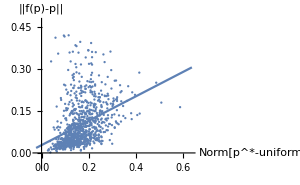

```mathematica
Show[{Plot[Evaluate@trend,{x,minx-0.05,maxx+0.05},PlotRange->{{minx-0.05,maxx+0.05},{miny-0.05,maxy+0.05}},AxesLabel->{TraditionalForm[Norm[ToExpression["p^*-uniform",TeXForm,HoldForm]]],"||f(p)-p||"}],ListPlot[subdata24]},ImageSize->300]
```

Distance of optimal report to fixed point against distance of fixed point to uniform

```mathematica
subdata23=Table[{data[[i]][[2]],data[[i]][[3]]},{i,1,Length@data}];
```

```mathematica
minx=Min[Table[subdata23[[i]][[1]],{i,1,Length@data}]]
```

0.0269433

```mathematica
maxx=Max[Table[subdata23[[i]][[1]],{i,1,Length@data}]]
```

0.586375

```mathematica
miny=Min[Table[subdata23[[i]][[2]],{i,1,Length@data}]]
```

0.0017994

```mathematica
maxy=Max[Table[subdata23[[i]][[2]],{i,1,Length@data}]]
```

0.95603

```mathematica
trend=Fit[subdata23,{1,x},x]
```

0.0451778+0.65777 x

```mathematica
Correlation[subdata23]
```

{{1.,0.272787},{0.272787,1.}}

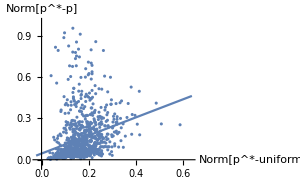

```mathematica
Show[{Plot[Evaluate@trend,{x,minx-0.05,maxx+0.05},PlotRange->{{minx-0.05,maxx+0.05},{miny-0.05,maxy+0.05}},AxesLabel->{TraditionalForm[Norm[ToExpression["p^*-uniform",TeXForm,HoldForm]]],TraditionalForm[Norm[ToExpression["p^*-p",TeXForm,HoldForm]]]}],ListPlot[subdata23]},ImageSize->300]
```

Accuracy of the optimal report against operator norm of A

```mathematica
subdata14=Table[{data[[i]][[1]],data[[i]][[4]]},{i,1,Length@data}];
```

```mathematica
minx=Min[Table[subdata14[[i]][[1]],{i,1,Length@data}]]
```

0.280956

```mathematica
maxx=Max[Table[subdata14[[i]][[1]],{i,1,Length@data}]]
```

0.870207

```mathematica
miny=Min[Table[subdata14[[i]][[2]],{i,1,Length@data}]]
```

0.00183539

```mathematica
maxy=Max[Table[subdata14[[i]][[2]],{i,1,Length@data}]]
```

0.421519

```mathematica
trend=Fit[subdata14,{1,x},x]
```

-0.0527396+0.275204 x

```mathematica
Correlation[subdata14]
```

{{1.,0.364372},{0.364372,1.}}

```mathematica
accbound[x_]:=If[S==BrierScore,Sqrt[(dim-1)/dim]*x,{}]
```

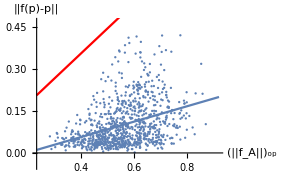

```mathematica
Show[{Plot[Evaluate@trend,{x,minx-0.05,maxx+0.05},PlotRange->{{minx-0.05,maxx+0.05},{miny-0.05,maxy+0.05}},AxesLabel->{Subscript["||"<>ToString[Subscript["f","A"],StandardForm]<>"||","op"],"||f(p)-p||"}],Plot[accbound[x],{x,minx-0.05,maxx+0.05},PlotStyle->Red],ListPlot[subdata14]},ImageSize->300]
```

Distance of optimal report to fixed point against operator norm of A

```mathematica
subdata13=Table[{data[[i]][[1]],data[[i]][[3]]},{i,1,Length@data}];
```

```mathematica
minx=Min[Table[subdata13[[i]][[1]],{i,1,Length@data}]]
```

0.280956

```mathematica
maxx=Max[Table[subdata13[[i]][[1]],{i,1,Length@data}]]
```

0.870207

```mathematica
miny=Min[Table[subdata13[[i]][[2]],{i,1,Length@data}]]
```

0.0017994

```mathematica
maxy=Max[Table[subdata13[[i]][[2]],{i,1,Length@data}]]
```

0.95603

```mathematica
trend=Fit[subdata13,{1,x},x]
```

-0.139112+0.525938 x

```mathematica
Correlation[subdata13]
```

{{1.,0.336762},{0.336762,1.}}

```mathematica
fpdistbound[x_]:=If[S==BrierScore,Sqrt[(dim-1)/dim]*(x/(1-x)),{}]
```

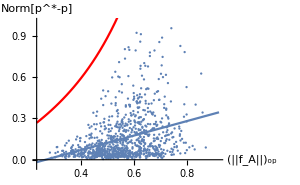

```mathematica
Show[{Plot[Evaluate@trend,{x,minx-0.05,maxx+0.05},PlotRange->{{minx-0.05,maxx+0.05},{miny-0.05,maxy+0.05}},AxesLabel->{Subscript["||"<>ToString[Subscript["f","A"],StandardForm]<>"||","op"],TraditionalForm[Norm[ToExpression["p^*-p",TeXForm,HoldForm]]]}],ListPlot[subdata13],Plot[fpdistbound[x],{x,minx-0.05,maxx+0.05},PlotStyle->Red]},ImageSize->300]
```

Accuracy of the optimal report against distance of optimal report to fixed point, along with the plot

```mathematica
subdata54=Table[{data[[i]][[5]],data[[i]][[4]]},{i,1,Length@data}];
```

```mathematica
minx=Min[Table[subdata54[[i]][[1]],{i,1,Length@data}]]
```

0.0262034

```mathematica
maxx=Max[Table[subdata54[[i]][[1]],{i,1,Length@data}]]
```

0.894427

```mathematica
miny=Min[Table[subdata54[[i]][[2]],{i,1,Length@data}]]
```

0.00183539

```mathematica
maxy=Max[Table[subdata54[[i]][[2]],{i,1,Length@data}]]
```

0.421519

```mathematica
trend=Fit[subdata54,{1,x},x]
```

-0.0143238+0.399585 x

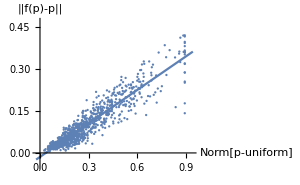

```mathematica
Show[{Plot[Evaluate@trend,{x,minx-0.05,maxx+0.05},PlotRange->{{minx-0.05,maxx+0.05},{miny-0.05,maxy+0.05}},AxesLabel->{TraditionalForm[Norm[ToExpression["p-uniform",TeXForm,HoldForm]]],"||f(p)-p||"}],ListPlot[subdata54]},ImageSize->300]
```

How correlated are the two measures of interest?

```mathematica
subdata34=Table[{data[[i]][[3]],data[[i]][[4]]},{i,1,Length@data}];
```

```mathematica
Correlation[subdata34]
```

{{1.,0.963114},{0.963114,1.}}

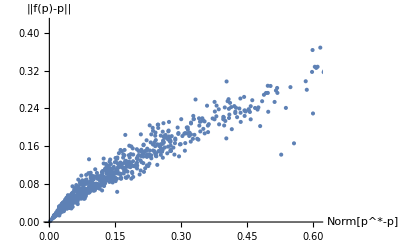

```mathematica
ListPlot[subdata34,AxesLabel->{Norm[ToExpression["p^*-p",TeXForm,HoldForm]],"||f(p)-p||"}]
```

What kinds of  are we sampling?

```mathematica
subdata12=Table[{data[[i]][[1]],data[[i]][[2]]},{i,1,Length@data}];
```

```mathematica
Correlation[subdata12]
```

{{1.,0.161424},{0.161424,1.}}

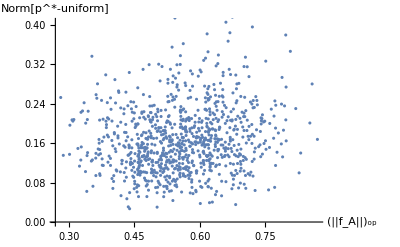

```mathematica
ListPlot[subdata12,AxesLabel->{Subscript["||"<>ToString[Subscript["f","A"],StandardForm]<>"||","op"],TraditionalForm[Norm[ToExpression["p^*-uniform",TeXForm,HoldForm]]]}]
```

Appendix A: Finding optimal reports with Mathematica in the Log Scoring rule case seems difficult

```mathematica
Clear[x];A=RandomA[3];Timing[TimeConstrained[Solve[D[LogScore[Array[x,3],A.Array[x,3]],x[1]]==0&&D[LogScore[Array[x,3],A.Array[x,3]],x[2]]==0&&D[LogScore[Array[x,3],A.Array[x,3]],x[3]]==0],300]]
```

{301.024,$Aborted}

```mathematica
A=RandomA[3];TimeConstrained[Maximize[{LogScore[Array[pmax,3],A.Array[pmax,3]],IsDistr[Array[pmax,3]]},Array[pmax,3]],500]
```

Maximize[{Log[pmax[3]] ((37 pmax[1])/82+(9 pmax[2])/35)+Log[pmax[2]] ((35 pmax[1])/82+(54 pmax[2])/175+(11 pmax[3])/85)+Log[pmax[1]] ((5 pmax[1])/41+(76 pmax[2])/175+(74 pmax[3])/85),pmax[1]+pmax[2]+pmax[3]==1&&NonNegative[pmax[1]]&&NonNegative[pmax[2]]&&NonNegative[pmax[3]]},{pmax[1],pmax[2],pmax[3]}]

Maximize[{Log[pmax[1]] ((411 pmax[1])/1000+(271 pmax[2])/500+(7 pmax[3])/200)+Log[pmax[3]] ((47 pmax[1])/200+(169 pmax[2])/500+(409 pmax[3])/1000)+Log[pmax[2]] ((177 pmax[1])/500+(3 pmax[2])/25+(139 pmax[3])/250),pmax[1]+pmax[2]+pmax[3]==1&&NonNegative[pmax[1]]&&NonNegative[pmax[2]]&&NonNegative[pmax[3]]},{pmax[1],pmax[2],pmax[3]}]